## Authors Informations

#### Authors: Huan Souza.b9* and A. C. Lehum.b9** Date: September 08, 2021 Filiation: Federal University of Pará.b9 Email: huan.souza@icen.ufpa.br*, lehum@ufpa.br**

# Quantum electrodynamics coupled to linearized gravity

```mathematica
Quit[]
```

To compute the diagrams, we have used FeynCalc [1], FeynArts [2], FeynHelpers [3] and TARCER [4].

```mathematica
description="Scalar electrodynamics coupled to linearized gravity";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts","TARCER","FeynHelpers"};
Get["FeynCalc`"]
$FAVerbose=0;
FCCheckVersion[9,3,0];
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (3 Aug 2020) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

TARCER 2.0, for more information see the accompanying publication. If you use TARCER in your research, please cite

• R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
(*We keep the scaleless B0 functions*)
$KeepLogDivergentScalelessIntegrals=True;
```

```mathematica
(*These are some definitions to make our outputs look better*)
MakeBoxes[mu,TraditionalForm]:="μ";
MakeBoxes[nu,TraditionalForm]:="ν";
MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
MakeBoxes[p3,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(3\)]\)";
MakeBoxes[p4,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(4\)]\)";
MakeBoxes[k1,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(1\)]\)";
MakeBoxes[k2,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(2\)]\)";
MakeBoxes[k3,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(3\)]\)";
MakeBoxes[k4,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(4\)]\)";
MakeBoxes[δλ,TraditionalForm]:="\!\(\*SubscriptBox[\(δ\), \(λ\)]\)";
```

```mathematica
(*Also, we make this defition because it is the definition used by TARCER*)
ScalarProduct[p,p]=p^2;
```

```mathematica
(*We are using models that we created and the directory with it should be inside the directory $UserBaseDirectory/Applications/FeynCalc/FeynArts/Models*)
```

```mathematica
(*Let us first initiate the models and create the topologies for the 1-loop and 2-loops diagrams*)
```

```mathematica
fields1={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_SQED_2loops","Einstein_SQED_2loops"}],Model->FileNameJoin[{"Einstein_SQED_2loops","Einstein_SQED_2loops"}]};
fields2={InsertionLevel->{Classes},GenericModel->FileNameJoin[{"Einstein_QED_2loops","Einstein_QED_2loops"}],Model->FileNameJoin[{"Einstein_QED_2loops","Einstein_QED_2loops"}]};
top1[i_,j_]:=CreateTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
topCT1[i_,j_]:=CreateCTTopologies[1,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
top2l[i_,j_]:=CreateTopologies[2,i->j,ExcludeTopologies->{Reducible},Adjacencies->{3,4,5}];
```

## Scalar-QED

## 1-loop counterterms

First, let us see if linearized gravity can change the behaviour of the electric charge β-function in one-loop order.

#### Scalar self-energy

```mathematica
sesc1=(InsertFields[#1,{S[1]}->{S[1]},Sequence@@fields1]&)[top1[1,1]];
sescCT1=(InsertFields[#1,{S[1]}->{S[1]},Sequence@@fields1]&)[topCT1[1,1]];
```

```mathematica
diag1=sesc1[[0]][Sequence@@sesc1,Sequence@@sescCT1];
```

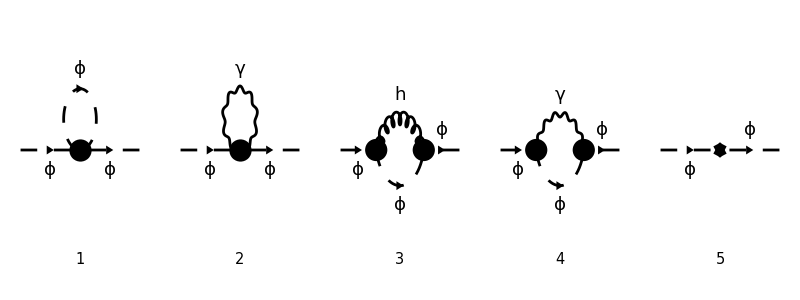

```mathematica
Paint[diag1,ColumnsXRows->{5,1},SheetHeader->{"Scalar self-energy"},Numbering->Simple,ImageSize->{800,300}];
```

```mathematica
(*To create the amplitude, we use CreateFeynAmp and choose to cut the external legs. Then, to convert the output to the FeynCalc form, we use FCFAConvert and choose the incoming momentum and the outgoing momentum to be p, the loop momentum to be k. Besides that, the option List->False sums the contributions of each diagram instead of make a list of them. The option SMP->True uses the standard model parameters. Also, we do this computation in D dimensions and the indeces of the polarization tensor are μ and ν. Finally, we explicity contract and other indeces and we substitute Z2 and Zm by SMP["d_phi"] and SMP["d_m"] respectively.*)
ampse1[0]=FCFAConvert[CreateFeynAmp[diag1,Truncated->True,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z2->1+SMP["d_phi"],Zm->1+SMP["d_m"]}]
```

-(ⅈ (D/k^2-((1-ξ_A) k^2)/((k^2)^2)) e^2)/(16 π^4)+(ⅈ (((1-ξ_A) ((k-p)·(k+p)) ((p-k)·(k+p)))/((k^2-m^2).((k-p)^2)^2)+(k+p)^2/((k^2-m^2).(k-p)^2)) e^2)/(16 π^4)-(ⅈ λ)/(16 π^4 (k^2-m^2))+1/(16 π^4)ⅈ (-1/2 ⅈ κ ((ⅈ κ D^2 m^2)/(4 (k^2-m^2).(k-p)^2)-(ⅈ κ D^2 (k·p))/(4 (k^2-m^2).(k-p)^2)-(ⅈ κ D m^2)/(2 (k^2-m^2).(k-p)^2)+(ⅈ κ D (k·p))/((k^2-m^2).(k-p)^2)+(2 ⅈ κ m^2 p^2)/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ m^2 p^2 ξ_h)/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ m^2 k^2)/((k^2-m^2).((k-p)^2)^2)-(4 ⅈ κ p^2 k^2)/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ m^2 ξ_h k^2)/((k^2-m^2).((k-p)^2)^2)+(4 ⅈ κ p^2 ξ_h k^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ (k·p))/((k^2-m^2).(k-p)^2)-(4 ⅈ κ m^2 (k·p))/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ p^2 (k·p))/((k^2-m^2).((k-p)^2)^2)+(4 ⅈ κ m^2 ξ_h (k·p))/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ p^2 ξ_h (k·p))/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ ξ_h k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)) m^2+1/2 ⅈ κ (k·p) ((ⅈ κ D^2 m^2)/(4 (k^2-m^2).(k-p)^2)-(ⅈ κ D^2 (k·p))/(4 (k^2-m^2).(k-p)^2)-(ⅈ κ D m^2)/(2 (k^2-m^2).(k-p)^2)+(ⅈ κ D (k·p))/((k^2-m^2).(k-p)^2)+(2 ⅈ κ m^2 p^2)/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ m^2 p^2 ξ_h)/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ m^2 k^2)/((k^2-m^2).((k-p)^2)^2)-(4 ⅈ κ p^2 k^2)/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ m^2 ξ_h k^2)/((k^2-m^2).((k-p)^2)^2)+(4 ⅈ κ p^2 ξ_h k^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ (k·p))/((k^2-m^2).(k-p)^2)-(4 ⅈ κ m^2 (k·p))/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ p^2 (k·p))/((k^2-m^2).((k-p)^2)^2)+(4 ⅈ κ m^2 ξ_h (k·p))/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ p^2 ξ_h (k·p))/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ ξ_h k^2 (k·p))/((k^2-m^2).((k-p)^2)^2))-ⅈ κ ((ⅈ κ p^4 k^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ p^4 ξ_h k^2)/((k^2-m^2).((k-p)^2)^2)+(ⅈ κ p^2 k^4)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ p^2 ξ_h k^4)/((k^2-m^2).((k-p)^2)^2)+(ⅈ κ p^2 (k·p)^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ p^2 ξ_h (k·p)^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ p^2 k^2)/(2 (k^2-m^2).(k-p)^2)-(2 ⅈ κ m^2 p^2 k^2)/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ m^2 p^2 ξ_h k^2)/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ m^2 p^2 (k·p))/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ m^2 p^2 ξ_h (k·p))/((k^2-m^2).((k-p)^2)^2)-(4 ⅈ κ p^2 k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)+(4 ⅈ κ p^2 ξ_h k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)+(ⅈ κ (k·p)^2)/(2 (k^2-m^2).(k-p)^2)-(ⅈ κ D (k·p)^2)/(4 (k^2-m^2).(k-p)^2)-(2 ⅈ κ m^2 (k·p)^2)/((k^2-m^2).((k-p)^2)^2)+(2 ⅈ κ m^2 ξ_h (k·p)^2)/((k^2-m^2).((k-p)^2)^2)+(ⅈ κ k^2 (k·p)^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ ξ_h k^2 (k·p)^2)/((k^2-m^2).((k-p)^2)^2)-(ⅈ κ m^2 (k·p))/(2 (k^2-m^2).(k-p)^2)+(ⅈ κ D m^2 (k·p))/(4 (k^2-m^2).(k-p)^2)+(2 ⅈ κ m^2 k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)-(2 ⅈ κ m^2 ξ_h k^2 (k·p))/((k^2-m^2).((k-p)^2)^2)))-ⅈ (ⅈ p^2 δ_ϕ-ⅈ m^2 δ_m)

```mathematica
(*Now, we use TID to convert the amplitude to the Passarino-Veltman integrals form.*)
ampse1[1]=TID[ampse1[0],k,ToPaVe->True]
```

-((m^2-p^2) B_0(0,0,0) (e^2 ξ_A-e^2-κ^2 m^2 ξ_h+κ^2 m^2))/(16 π^2)-((m^2-p^2)^2 C_0(0,p^2,p^2,0,0,m^2) (e^2 ξ_A-e^2-κ^2 m^2 ξ_h+κ^2 m^2))/(16 π^2)+(B_0(p^2,0,m^2) (-D^2 κ^2 m^4+2 D^2 κ^2 m^2 p^2-D^2 κ^2 p^4-2 D κ^2 m^4-4 D κ^2 m^2 p^2+6 D κ^2 p^4-64 e^2 m^2-64 e^2 p^2+8 κ^2 m^4+16 κ^2 m^2 p^2-8 κ^2 p^4))/(512 π^2)+(A_0(m^2) (-3 D^2 κ^2 m^2+D^2 κ^2 p^2+10 D κ^2 m^2-6 D κ^2 p^2+32 e^2+32 λ-8 κ^2 m^2+8 κ^2 p^2))/(512 π^2)+m^2 (-δ_m)+p^2 δ_ϕ

```mathematica
(*To evaluate this result, we are using the function from FeynHelpers, PaXEvaluate*)
ampse1[2]=PaXEvaluate[ampse1[1]]
```

(-2 κ^2 m^4+κ^2 ξ_h m^4+2 κ^2 p^2 m^2-ξ_A e^2 m^2+λ m^2-κ^2 p^2 ξ_h m^2-3 p^2 e^2+p^2 ξ_A e^2)/(16 ε π^2)+1/(128 p^2 π^2)(-4 κ^2 log(m^2/(m^2-p^2)) m^6+8 κ^2 ξ_h log(m^2/(m^2-p^2)) m^6+16 κ^2 ℽ p^2 m^4-8 ξ_A log(m^2/(m^2-p^2)) e^2 m^4+24 log(m^2/(m^2-p^2)) e^2 m^4-8 κ^2 ℽ p^2 ξ_h m^4-12 κ^2 p^2 log(m^2/(m^2-p^2)) m^4-12 κ^2 p^2 log(μ^2/m^2) m^4+8 κ^2 p^2 ξ_h log(μ^2/m^2) m^4-4 κ^2 p^2 log(μ^2/(m^2 π)) m^4+12 κ^2 p^2 log(π) m^4-8 κ^2 p^2 ξ_h log(π) m^4+9 κ^2 p^4 m^2-16 κ^2 ℽ p^4 m^2+8 λ p^2 m^2-8 λ ℽ p^2 m^2-24 p^2 e^2 m^2+8 ℽ p^2 ξ_A e^2 m^2-8 p^2 log(μ^2/m^2) e^2 m^2-8 p^2 ξ_A log(μ^2/m^2) e^2 m^2+8 p^2 log(μ^2/(m^2 π)) e^2 m^2+8 p^2 log(π) e^2 m^2+8 p^2 ξ_A log(π) e^2 m^2+8 κ^2 ℽ p^4 ξ_h m^2+16 κ^2 p^4 log(m^2/(m^2-p^2)) m^2-8 κ^2 p^4 ξ_h log(m^2/(m^2-p^2)) m^2+16 κ^2 p^4 log(μ^2/m^2) m^2-8 κ^2 p^4 ξ_h log(μ^2/m^2) m^2+8 λ p^2 log(μ^2/(m^2 π)) m^2-128 p^2 π^2 δ_m m^2-16 κ^2 p^4 log(π) m^2+8 κ^2 p^4 ξ_h log(π) m^2+κ^2 p^6+24 ℽ p^4 e^2-32 p^4 e^2-8 ℽ p^4 ξ_A e^2-24 p^4 log(m^2/(m^2-p^2)) e^2+8 p^4 ξ_A log(m^2/(m^2-p^2)) e^2-24 p^4 log(μ^2/m^2) e^2+8 p^4 ξ_A log(μ^2/m^2) e^2+24 p^4 log(π) e^2-8 p^4 ξ_A log(π) e^2+128 p^4 π^2 δ_ϕ)

```mathematica
(*In order to compute the counterterm, we only need the divegent part of it*)
ampse1[3]=SelectNotFree2[ampse1[2],{Epsilon,SMP["d_phi"],SMP["d_m"]}]
```

(-e^2 m^2 ξ_A+e^2 p^2 ξ_A-3 e^2 p^2+κ^2 m^4 ξ_h-κ^2 m^2 p^2 ξ_h-2 κ^2 m^4+λ m^2+2 κ^2 m^2 p^2)/(16 π^2 ε)+m^2 (-δ_m)+p^2 δ_ϕ

```mathematica
(*Finally, we solve this order by order in the external momentum*)
solution1=Flatten[Solve[SelectNotFree2[ampse1[3],p]==0,SMP["d_phi"]]]
solution2=Flatten[Solve[SelectFree2[ampse1[3],p]==0,SMP["d_m"]]]
```

{δ_ϕ→(-e^2 ξ_A+3 e^2+κ^2 m^2 ξ_h-2 κ^2 m^2)/(16 π^2 ε)}

{δ_m→(-e^2 ξ_A+κ^2 m^2 ξ_h+λ-2 κ^2 m^2)/(16 π^2 ε)}

```mathematica
Subscript[δ,ϕ]=SMP["d_phi"]/.solution1
Subscript[δ,m]=SMP["d_m"]/.solution2
```

(-e^2 ξ_A+3 e^2+κ^2 m^2 ξ_h-2 κ^2 m^2)/(16 π^2 ε)

(-e^2 ξ_A+κ^2 m^2 ξ_h+λ-2 κ^2 m^2)/(16 π^2 ε)

#### Photon self-energy

```mathematica
(*Now we proceed to compute the photon self-energy*)
```

```mathematica
seph1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[top1[1,1]];
sephCT1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[topCT1[1,1]];
```

```mathematica
(*Here, we put together the diagrams with and without counterterms*)
diag2=seph1[[0]][Sequence@@seph1,Sequence@@sephCT1];
```

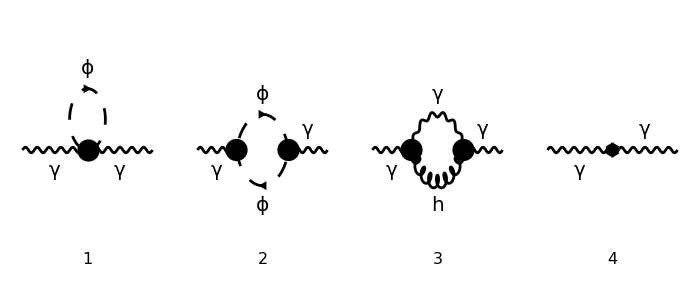

```mathematica
Paint[diag2,ColumnsXRows->{4,1},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{700,300}];
```

```mathematica
(*Here, we compute the diagrams in the same manner as we did for the scalar self-energy*)
ampse2[0]=FCFAConvert[CreateFeynAmp[diag2,Truncated->True,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z3->1+SMP["d_A"]}]
```

-(3 ⅈ κ^2 p^4 g^μν)/(16 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 p^4 g^μν)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D p^4 g^μν)/(64 π^4 k^2.(k-p)^2)+(3 ⅈ κ^2 p^4 k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 D p^4 k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)-(3 ⅈ κ^2 p^4 ξ_h k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 D p^4 ξ_h k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^4 g^μν k^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^4 ξ_h g^μν k^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^2 g^μν k^4)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^2 ξ_h g^μν k^4)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^2 g^μν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^2 ξ_h g^μν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^2 k^μ k^ν)/(4 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 p^2 k^μ k^ν)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D p^2 k^μ k^ν)/(64 π^4 k^2.(k-p)^2)+(3 ⅈ κ^2 p^2 p^μ p^ν)/(16 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 p^2 p^μ p^ν)/(128 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D p^2 p^μ p^ν)/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^2 g^μν k^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^2 k^μ k^ν k^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^2 ξ_h k^μ k^ν k^2)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^2 p^μ p^ν k^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^2 ξ_h p^μ p^ν k^2)/(8 π^4 (k-p)^2.(k^2)^2)+(3 ⅈ κ^2 p^2 g^μν (k·p))/(8 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 p^2 g^μν (k·p))/(64 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D p^2 g^μν (k·p))/(32 π^4 k^2.(k-p)^2)-(ⅈ κ^2 p^2 k^μ k^ν (k·p))/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^2 ξ_h k^μ k^ν (k·p))/(8 π^4 (k-p)^2.(k^2)^2)-(3 ⅈ κ^2 p^2 p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 D p^2 p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(3 ⅈ κ^2 p^2 ξ_h p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 D p^2 ξ_h p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(3 ⅈ κ^2 p^2 k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 D p^2 k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(3 ⅈ κ^2 p^2 ξ_h k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 D p^2 ξ_h k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^2 g^μν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^2 ξ_h g^μν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)-g^μν δ_A p^2-(ⅈ κ^2 g^μν (k·p)^3)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h g^μν (k·p)^3)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^μ p^ν k^4)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h p^μ p^ν k^4)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 g^μν (k·p)^2)/(4 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 g^μν (k·p)^2)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D g^μν (k·p)^2)/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^μ k^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h p^μ k^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 k^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h k^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 D p^μ p^ν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h p^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 D ξ_h p^μ p^ν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 g^μν k^2 (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h g^μν k^2 (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ g^μν e^2)/(8 π^4 (k^2-m^2))-(ⅈ k^μ k^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ (k-p)^μ k^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))+(ⅈ k^μ (p-k)^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))+(ⅈ (k-p)^μ (p-k)^ν e^2)/(16 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ κ^2 p^μ p^ν k^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^μ k^ν (k·p))/(4 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 p^μ k^ν (k·p))/(128 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D p^μ k^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 k^μ p^ν (k·p))/(4 π^4 k^2.(k-p)^2)+(ⅈ κ^2 D^2 k^μ p^ν (k·p))/(128 π^4 k^2.(k-p)^2)-(7 ⅈ κ^2 D k^μ p^ν (k·p))/(64 π^4 k^2.(k-p)^2)-(3 ⅈ κ^2 p^μ p^ν (k·p))/(8 π^4 k^2.(k-p)^2)-(ⅈ κ^2 D^2 p^μ p^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(7 ⅈ κ^2 D p^μ p^ν (k·p))/(32 π^4 k^2.(k-p)^2)-(ⅈ κ^2 p^μ k^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h p^μ k^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 k^μ p^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h k^μ p^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^μ p^ν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h p^μ p^ν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)+p^μ p^ν δ_A

```mathematica
(*Now, we use TID to convert the amplitude to the Passarino-Veltman integrals form.*)
ampse2[1]=TID[ampse2[0],k,ToPaVe->True]
```

-(κ^2 (2-D) C_0(0,p^2,p^2,0,0,0) (1-ξ_h) (g^μν p^2-(1-D) p^μ p^ν-D p^μ p^ν) p^4)/(64 (1-D) π^2)+(κ^2 (2-D) B_0(0,0,0) (1-ξ_h) (g^μν p^2-(1-D) p^μ p^ν-D p^μ p^ν) p^2)/(64 (1-D) π^2)+1/(512 (1-D) π^2)κ^2 B_0(p^2,0,0) (-p^μ p^ν D^3+(1-D) p^2 g^μν D^2+p^2 g^μν D^2-2 (1-D) p^μ p^ν D^2+16 ξ_h p^μ p^ν D^2-2 p^μ p^ν D^2-14 (1-D) p^2 g^μν D-30 p^2 g^μν D+16 p^2 ξ_h g^μν D+12 (1-D) p^μ p^ν D+16 (1-D) ξ_h p^μ p^ν D-64 ξ_h p^μ p^ν D+32 p^μ p^ν D+32 (1-D) p^2 g^μν+64 p^2 g^μν-32 p^2 ξ_h g^μν-32 (1-D) p^μ p^ν-32 (1-D) ξ_h p^μ p^ν+64 ξ_h p^μ p^ν-64 p^μ p^ν) p^2-(p^2 g^μν-p^μ p^ν) δ_A-(A_0(m^2) ((1-D) g^μν p^2+g^μν p^2+D p^μ p^ν-2 p^μ p^ν) e^2)/(8 (1-D) π^2 p^2)-(B_0(p^2,m^2,m^2) (-g^μν p^4+4 m^2 g^μν p^2+(1-D) p^μ p^ν p^2+D p^μ p^ν p^2-4 m^2 p^μ p^ν) e^2)/(16 (1-D) π^2 p^2)

```mathematica
(*To evaluate this result, we are using the function from FeynHelpers, PaXEvaluate*)
ampse2[2]=PaXEvaluate[ampse2[1]]
```

1/(576 π^2 p^2)g^μν (-576 π^2 p^4 δ_A-12 e^2 p^4 log(μ^2/m^2)+96 e^2 m^2 p^2-12 e^2 p^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))+48 e^2 m^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))+12 ℽ e^2 p^4-32 e^2 p^4+12 e^2 p^4 log(π)-18 κ^2 p^6 ξ_h+18 ℽ κ^2 p^6 ξ_h+18 κ^2 p^6 log(π) ξ_h-18 κ^2 p^6 ξ_h log(-μ^2/p^2)+17 κ^2 p^6-12 ℽ κ^2 p^6-12 κ^2 p^6 log(π)+12 κ^2 p^6 log(-μ^2/p^2))+1/(576 π^2 p^4)p^μ p^ν (576 π^2 p^4 δ_A+12 e^2 p^4 log(μ^2/m^2)-96 e^2 m^2 p^2+12 e^2 p^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))-48 e^2 m^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))-12 ℽ e^2 p^4+32 e^2 p^4-12 e^2 p^4 log(π)+18 κ^2 p^6 ξ_h-18 ℽ κ^2 p^6 ξ_h-18 κ^2 p^6 log(π) ξ_h+18 κ^2 p^6 ξ_h log(-μ^2/p^2)-17 κ^2 p^6+12 ℽ κ^2 p^6+12 κ^2 p^6 log(π)-12 κ^2 p^6 log(-μ^2/p^2))-(p^2 g^μν (2 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2))/(96 π^2 ε)+(p^μ p^ν (2 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2))/(96 π^2 ε)

```mathematica
(*In order to compute the counterterm, we only need the divegent part of it*)
ampse2[3]=SelectNotFree2[ampse2[2],{Epsilon,SMP["d_A"]}]//Factor
```

-((p^2 g^μν-p^μ p^ν) (96 π^2 ε δ_A+2 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2))/(96 π^2 ε)

```mathematica
(*Once all terms are multiplied by Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]-Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*Pair[Momentum[p,D],Momentum[p,D]], to compute the counterterms, we only need Π(p).*)
ampse2[4]=Coefficient[ampse2[3],(p^2 Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]] Pair[LorentzIndex[nu,D],Momentum[p,D]])]//Simplify
```

-(96 π^2 ε δ_A+2 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2)/(96 π^2 ε)

```mathematica
(*Finally, we find the countertem. Here, we will only compute the counterterm for the Maxwell term. The HO counterterm can be easily computed using the terms proportional to p^2 in the above expression.*)
solution3=Flatten[Solve[SelectFree2[ampse2[4],p]==0,SMP["d_A"]]]
```

{δ_A→-e^2/(48 π^2 ε)}

```mathematica
Subscript[δ,A]=SMP["d_A"]/.solution3
```

-e^2/(48 π^2 ε)

We can notice that there is no contribution of order κ.b2. Then, linearized gravity does not contribute to the electrical charge β-function in one-loop order.

#### Photon-Scalar vertex

```mathematica
vertexsc1=(InsertFields[#1,{V[1]}->{S[1],-S[1]},Sequence@@fields1]&)[top1[1,2]];
vertexscCT1=(InsertFields[#1,{V[1]}->{S[1],-S[1]},Sequence@@fields1]&)[topCT1[1,2]];
```

```mathematica
diag3=vertexsc1[[0]][Sequence@@vertexsc1,Sequence@@vertexscCT1];
```

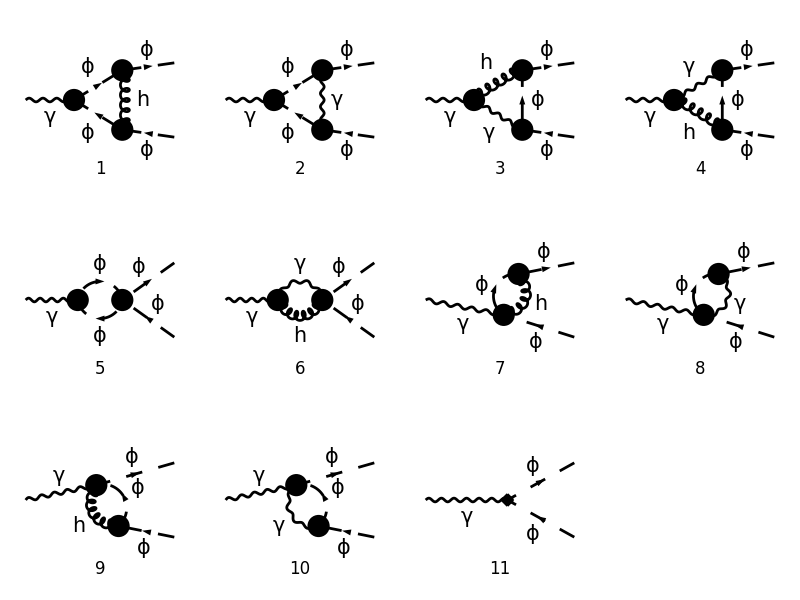

```mathematica
Paint[diag3,ColumnsXRows->{4,3},SheetHeader->{"Photon-Scalar vertex"},Numbering->Simple,ImageSize->{800,600}];
```

```mathematica
ampVertexsc[0]=FCFAConvert[CreateFeynAmp[diag3,Truncated->True,GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{p2,p3},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z1->1+SMP["d_e"]}]
```

(ⅈ κ^2 D^2 m^4 k^μ e)/(64 π^4 (k^2-m^2).(k-p_2)^2.((k-p_2-p_3)^2-m^2))-(ⅈ κ^2 D m^4 k^μ e)/(32 π^4 (k^2-m^2).(k-1)^2.((1)^2-m^2))-(ⅈ κ^2 D^2 m^4 26^μ e)/(128 π^4 (k^2-m^2).1^2.(1))+1026+p_3^μ δ_e e
 |  |  |  |

```mathematica
(*Here, we set UsePaVeBasis->True to simplify our computation*)
ampVertexsc[1]=TID[ampVertexsc[0],k,ToPaVe->True,UsePaVeBasis->True]
```

-(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) D_1(p_3^2,0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e m^4)/(4 π^2)-(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) D_2(p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,p_2^2,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e m^4)/(4 π^2)-(κ^2 C_0(p_2^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,m^2,0) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) e m^2)/(8 π^2)-(κ^2 D_0(0,p_2^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,m^2,0) (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (m^2-p_2^2) e m^2)/(8 π^2)-(κ^2 D_0(0,p_3^2,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,m^2,0) (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (m^2-p_3^2) e m^2)/(8 π^2)+(κ^2 (2-D) (4-D) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) C_1(p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,m^2,0,0) e m^2)/(64 π^2)+(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) p_2^2 D_1(p_2^2,0,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e m^2)/(4 π^2)-(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (p_2·p_3) D_1(p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,0,p_3^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e m^2)/(4 π^2)+(κ^2 (2-D) (4-D) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) C_2(p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,m^2,0,0) e m^2)/(64 π^2)+(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) p_3^2 D_2(p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,0,p_3^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e m^2)/(4 π^2)-(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (p_2·p_3) D_3(p_2^2,0,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e m^2)/(4 π^2)-(κ^2 A_0(m^2) (p_2^μ D^2-3 p_3^μ D^2-6 p_2^μ D+18 p_3^μ D+16 p_2^μ-32 p_3^μ) e)/(512 π^2)-(κ^2 B_0(p_2^2+2 (p_2·p_3)+p_3^2,0,0) (D^2-16 D-48 ξ_h+84) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) e)/(128 π^2)+(κ^2 B_0(p_2^2+2 (p_2·p_3)+p_3^2,0,0) (D^2-12 D-8 ξ_h+28) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) e)/(128 π^2)-(κ^2 (D^2-8 D+20) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (m^2+p_3^2) C_1(p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2,m^2,0,0) e)/(128 π^2)-1/(16 π^2)κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (m^4-p_2^2 m^2-4 (p_2·p_3) m^2+p_3^2 m^2-p_2^2 p_3^2) D_1(p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,p_2^2,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e-(κ^2 (D^2-8 D+20) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (m^2+p_2^2) C_2(p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2,m^2,0,0) e)/(128 π^2)-1/(16 π^2)κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (m^4+p_2^2 m^2-4 (p_2·p_3) m^2-p_3^2 m^2-p_2^2 p_3^2) D_3(p_3^2,0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,0,0) e+(κ^2 (D+4) (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) C_00(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0) e)/(8 π^2)+(κ^2 (1-ξ_h) (p_3^μ (p_1·p_2)-p_2^μ (p_1·p_3)) (p_2^2+2 (p_2·p_3)+p_3^2) C_22(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0) e)/(2 π^2)+1/(512 π^2)B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (p_2^μ+p_3^μ) e (-3 D^2 m^2 κ^2+10 D m^2 κ^2-8 m^2 κ^2+D^2 p_2^2 κ^2-6 D p_2^2 κ^2+16 p_2^2 κ^2+16 (p_2·p_3) κ^2+8 p_3^2 κ^2+32 e^2+32 λ)-1/(512 π^2)B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (p_2^μ+p_3^μ) e (-3 D^2 m^2 κ^2+10 D m^2 κ^2-8 m^2 κ^2+D^2 p_2^2 κ^2-6 D p_2^2 κ^2+16 p_2^2 κ^2-D^2 (p_2·p_3) κ^2+6 D (p_2·p_3) κ^2+8 (p_2·p_3) κ^2-D^2 p_3^2 κ^2+6 D p_3^2 κ^2+32 e^2+32 λ)-1/(32 π^2)D_0(0,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,p_2^2,p_3^2,0,0,m^2,m^2) (p_2^μ-p_3^μ) (m^2-p_2^2) (m^2-p_3^2) e (2 m^2 κ^2-2 m^2 ξ_h κ^2+ξ_h p_2^2 κ^2-p_2^2 κ^2+2 ξ_h (p_2·p_3) κ^2-2 (p_2·p_3) κ^2+ξ_h p_3^2 κ^2-p_3^2 κ^2+2 ξ_A e^2-2 e^2)-1/(16 π^2)p_2^μ (m^2-p_2^2) (m^2-p_3^2) D_2(0,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,p_2^2,p_3^2,0,0,m^2,m^2) e (2 m^2 κ^2-2 m^2 ξ_h κ^2+ξ_h p_2^2 κ^2-p_2^2 κ^2+2 ξ_h (p_2·p_3) κ^2-2 (p_2·p_3) κ^2+ξ_h p_3^2 κ^2-p_3^2 κ^2+2 ξ_A e^2-2 e^2)+1/(16 π^2)p_3^μ (m^2-p_2^2) (m^2-p_3^2) D_3(0,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,p_2^2,p_3^2,0,0,m^2,m^2) e (2 m^2 κ^2-2 m^2 ξ_h κ^2+ξ_h p_2^2 κ^2-p_2^2 κ^2+2 ξ_h (p_2·p_3) κ^2-2 (p_2·p_3) κ^2+ξ_h p_3^2 κ^2-p_3^2 κ^2+2 ξ_A e^2-2 e^2)-1/(512 π^2)B_0(p_2^2,0,m^2) e (D^2 m^2 p_2^μ κ^2-2 D m^2 p_2^μ κ^2+16 m^2 p_2^μ κ^2-D^2 m^2 p_3^μ κ^2+2 D m^2 p_3^μ κ^2-8 m^2 p_3^μ κ^2+16 m^2 ξ_h p_3^μ κ^2-D^2 p_2^μ p_2^2 κ^2+6 D p_2^μ p_2^2 κ^2+D^2 p_3^μ p_2^2 κ^2-6 D p_3^μ p_2^2 κ^2-16 ξ_h p_3^μ p_2^2 κ^2+24 p_3^μ p_2^2 κ^2-16 p_2^μ (p_2·p_3) κ^2-16 p_3^μ (p_2·p_3) κ^2-96 p_2^μ e^2-32 p_3^μ e^2)-1/(512 π^2)B_0(p_3^2,0,m^2) e (D^2 m^2 p_2^μ κ^2-2 D m^2 p_2^μ κ^2+8 m^2 p_2^μ κ^2-16 m^2 ξ_h p_2^μ κ^2-D^2 m^2 p_3^μ κ^2+2 D m^2 p_3^μ κ^2-16 m^2 p_3^μ κ^2+16 p_2^μ (p_2·p_3) κ^2+16 p_3^μ (p_2·p_3) κ^2-D^2 p_2^μ p_3^2 κ^2+6 D p_2^μ p_3^2 κ^2+16 ξ_h p_2^μ p_3^2 κ^2-24 p_2^μ p_3^2 κ^2+D^2 p_3^μ p_3^2 κ^2-6 D p_3^μ p_3^2 κ^2+32 p_2^μ e^2+96 p_3^μ e^2)-1/(32 π^2)B_0(0,0,0) e (m^2 p_2^μ κ^2-m^2 ξ_h p_2^μ κ^2-m^2 p_3^μ κ^2+m^2 ξ_h p_3^μ κ^2-ξ_h p_3^μ p_2^2 κ^2+p_3^μ p_2^2 κ^2+2 ξ_h p_2^μ (p_2·p_3) κ^2-2 p_2^μ (p_2·p_3) κ^2-2 ξ_h p_3^μ (p_2·p_3) κ^2+2 p_3^μ (p_2·p_3) κ^2+ξ_h p_2^μ p_3^2 κ^2-p_2^μ p_3^2 κ^2+2 ξ_A p_2^μ e^2-2 p_2^μ e^2-2 ξ_A p_3^μ e^2+2 p_3^μ e^2)-1/(32 π^2)C_0(0,p_3^2,p_3^2,0,0,m^2) (m^2-p_3^2) e (2 m^2 p_2^μ κ^2-2 m^2 ξ_h p_2^μ κ^2-m^2 p_3^μ κ^2+m^2 ξ_h p_3^μ κ^2+ξ_h p_2^μ p_2^2 κ^2-p_2^μ p_2^2 κ^2-ξ_h p_3^μ p_2^2 κ^2+p_3^μ p_2^2 κ^2+2 ξ_h p_2^μ (p_2·p_3) κ^2-2 p_2^μ (p_2·p_3) κ^2-2 ξ_h p_3^μ (p_2·p_3) κ^2+2 p_3^μ (p_2·p_3) κ^2+ξ_h p_2^μ p_3^2 κ^2-p_2^μ p_3^2 κ^2+2 ξ_A p_2^μ e^2-2 p_2^μ e^2-2 ξ_A p_3^μ e^2+2 p_3^μ e^2)-1/(32 π^2)C_0(0,p_2^2,p_2^2,0,0,m^2) (m^2-p_2^2) e (m^2 p_2^μ κ^2-m^2 ξ_h p_2^μ κ^2-2 m^2 p_3^μ κ^2+2 m^2 ξ_h p_3^μ κ^2-ξ_h p_3^μ p_2^2 κ^2+p_3^μ p_2^2 κ^2+2 ξ_h p_2^μ (p_2·p_3) κ^2-2 p_2^μ (p_2·p_3) κ^2-2 ξ_h p_3^μ (p_2·p_3) κ^2+2 p_3^μ (p_2·p_3) κ^2+ξ_h p_2^μ p_3^2 κ^2-p_2^μ p_3^2 κ^2-ξ_h p_3^μ p_3^2 κ^2+p_3^μ p_3^2 κ^2+2 ξ_A p_2^μ e^2-2 p_2^μ e^2-2 ξ_A p_3^μ e^2+2 p_3^μ e^2)+1/(512 π^2)C_0(p_2^2,p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,m^2,0,m^2) (p_2^μ-p_3^μ) e (8 κ^2 m^4-κ^2 D^2 m^4-2 κ^2 D m^4-64 e^2 m^2-8 κ^2 p_2^2 m^2+κ^2 D^2 p_2^2 m^2-2 κ^2 D p_2^2 m^2-32 κ^2 (p_2·p_3) m^2-8 κ^2 p_3^2 m^2+κ^2 D^2 p_3^2 m^2-2 κ^2 D p_3^2 m^2+32 κ^2 (p_2·p_3)^2+32 p_2^2 e^2+128 (p_2·p_3) e^2+32 p_3^2 e^2+16 κ^2 p_2^2 (p_2·p_3)-8 κ^2 p_2^2 p_3^2-κ^2 D^2 p_2^2 p_3^2+6 κ^2 D p_2^2 p_3^2+16 κ^2 (p_2·p_3) p_3^2)+1/(256 π^2)p_2^μ C_1(p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,0,m^2,m^2) e (8 κ^2 m^4-κ^2 D^2 m^4-2 κ^2 D m^4-64 e^2 m^2-8 κ^2 p_2^2 m^2+κ^2 D^2 p_2^2 m^2-2 κ^2 D p_2^2 m^2-32 κ^2 (p_2·p_3) m^2-8 κ^2 p_3^2 m^2+κ^2 D^2 p_3^2 m^2-2 κ^2 D p_3^2 m^2+32 κ^2 (p_2·p_3)^2+32 p_2^2 e^2+128 (p_2·p_3) e^2+32 p_3^2 e^2+16 κ^2 p_2^2 (p_2·p_3)-8 κ^2 p_2^2 p_3^2-κ^2 D^2 p_2^2 p_3^2+6 κ^2 D p_2^2 p_3^2+16 κ^2 (p_2·p_3) p_3^2)-1/(256 π^2)p_3^μ C_2(p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,p_3^2,0,m^2,m^2) e (8 κ^2 m^4-κ^2 D^2 m^4-2 κ^2 D m^4-64 e^2 m^2-8 κ^2 p_2^2 m^2+κ^2 D^2 p_2^2 m^2-2 κ^2 D p_2^2 m^2-32 κ^2 (p_2·p_3) m^2-8 κ^2 p_3^2 m^2+κ^2 D^2 p_3^2 m^2-2 κ^2 D p_3^2 m^2+32 κ^2 (p_2·p_3)^2+32 p_2^2 e^2+128 (p_2·p_3) e^2+32 p_3^2 e^2+16 κ^2 p_2^2 (p_2·p_3)-8 κ^2 p_2^2 p_3^2-κ^2 D^2 p_2^2 p_3^2+6 κ^2 D p_2^2 p_3^2+16 κ^2 (p_2·p_3) p_3^2)-1/(128 π^2)e (-8 m^2 p_2^μ (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 m^2 ξ_h p_2^μ (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 m^2 p_3^μ (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2-8 m^2 ξ_h p_3^μ (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2-8 ξ_h p_2^μ p_2^2 (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 p_2^μ p_2^2 (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 ξ_h p_3^μ p_2^2 (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2-8 p_3^μ p_2^2 (p_2·p_3) (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2-8 m^2 p_2^μ p_3^2 (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 m^2 ξ_h p_2^μ p_3^2 (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2-8 ξ_h p_2^μ p_2^2 p_3^2 (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 p_2^μ p_2^2 p_3^2 (-C_0(0,p_2^2,p_2^2,0,0,m^2)-2 C_1(0,p_2^2,p_2^2,0,0,m^2)) κ^2+8 m^2 p_3^μ p_2^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-8 m^2 ξ_h p_3^μ p_2^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-8 m^2 p_2^μ (p_2·p_3) (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2+8 m^2 ξ_h p_2^μ (p_2·p_3) (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2+8 m^2 p_3^μ (p_2·p_3) (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-8 m^2 ξ_h p_3^μ (p_2·p_3) (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2+8 ξ_h p_3^μ p_2^2 p_3^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-8 p_3^μ p_2^2 p_3^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-8 ξ_h p_2^μ (p_2·p_3) p_3^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2+8 p_2^μ (p_2·p_3) p_3^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2+8 ξ_h p_3^μ (p_2·p_3) p_3^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-8 p_3^μ (p_2·p_3) p_3^2 (-C_0(0,p_3^2,p_3^2,0,0,m^2)-2 C_1(0,p_3^2,p_3^2,0,0,m^2)) κ^2-16 m^2 p_3^μ (p_1·p_2) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+16 m^2 ξ_h p_3^μ (p_1·p_2) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+16 m^2 p_2^μ (p_1·p_3) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-16 m^2 ξ_h p_2^μ (p_1·p_3) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+8 ξ_h p_3^μ (p_1·p_2) p_2^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-8 p_3^μ (p_1·p_2) p_2^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-8 ξ_h p_2^μ (p_1·p_3) p_2^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+8 p_2^μ (p_1·p_3) p_2^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+32 ξ_h p_3^μ (p_1·p_2) (p_2·p_3) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-32 p_3^μ (p_1·p_2) (p_2·p_3) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-32 ξ_h p_2^μ (p_1·p_3) (p_2·p_3) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+32 p_2^μ (p_1·p_3) (p_2·p_3) (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+8 ξ_h p_3^μ (p_1·p_2) p_3^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-8 p_3^μ (p_1·p_2) p_3^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2-8 ξ_h p_2^μ (p_1·p_3) p_3^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+8 p_2^μ (p_1·p_3) p_3^2 (-C_0(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)-2 C_1(0,p_2^2+2 (p_2·p_3)+p_3^2,p_2^2+2 (p_2·p_3)+p_3^2,0,0,0)) κ^2+4 p_2^μ p_2^2 ((B_0(p_2^2,0,m^2) (m^2-p_2^2))/(2 p_2^2)-(A_0(m^2))/(2 p_2^2)) κ^2+D^2 p_3^μ (-(A_0(m^2))/(2 (1-D))-(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-p_2^2-2 (p_2·p_3)-p_3^2))/(4 (1-D))) κ^2-6 D p_3^μ (-(A_0(m^2))/(2 (1-D))-(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-p_2^2-2 (p_2·p_3)-p_3^2))/(4 (1-D))) κ^2+8 p_3^μ (-(A_0(m^2))/(2 (1-D))-(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-p_2^2-2 (p_2·p_3)-p_3^2))/(4 (1-D))) κ^2-4 p_3^μ p_3^2 ((B_0(p_3^2,0,m^2) (m^2-p_3^2))/(2 p_3^2)-(A_0(m^2))/(2 p_3^2)) κ^2+D^2 p_2^μ (p_2·p_3) (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2-6 D p_2^μ (p_2·p_3) (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+8 p_2^μ (p_2·p_3) (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+D^2 p_3^μ (p_2·p_3) (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2-6 D p_3^μ (p_2·p_3) (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+8 p_3^μ (p_2·p_3) (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+D^2 p_2^μ p_3^2 (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2-6 D p_2^μ p_3^2 (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+8 p_2^μ p_3^2 (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+D^2 p_3^μ p_3^2 (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2-6 D p_3^μ p_3^2 (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+8 p_3^μ p_3^2 (((2-D) A_0(m^2))/(2 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))+(B_0(p_2^2+2 (p_2·p_3)+p_3^2,m^2,m^2) (4 m^2-D p_2^2-2 D (p_2·p_3)-D p_3^2))/(4 (1-D) (p_2^2+2 (p_2·p_3)+p_3^2))) κ^2+128 π^2 p_2^μ δ_e-128 π^2 p_3^μ δ_e)

```mathematica
(*This expression is very complicated and use PaXEvaluate to compute the integrals would take a long time. Therefore, we use here PaVeUVPart to take only the UV divergences from it*)
ampVertexsc[2]=Simplify[(SelectNotFree2[#1,{Epsilon,SMP["d_e"]}]&)[Normal[(Series[#1,{Epsilon,0,0}]&)[(FCReplaceD[#1,D->4-2*Epsilon]&)[DiracSimplify[PaVeUVPart[ampVertexsc[1]]]]]]]]
```

1/(16 π^2 ε)e (p_2^μ (-e^2 ξ_A+3 e^2-16 π^2 ε δ_e+κ^2 ξ_h (m^2-p_1·p_3-p_2·p_3-p_3^2)-2 κ^2 m^2+κ^2 (p_1·p_3)+κ^2 (p_2·p_3)+κ^2 p_3^2)+p_3^μ (e^2 ξ_A-3 e^2+16 π^2 ε δ_e+κ^2 ξ_h (-m^2+p_1·p_2+p_2·p_3+p_2^2)+2 κ^2 m^2-κ^2 (p_1·p_2)-κ^2 p_2^2-κ^2 (p_2·p_3)))

```mathematica
(*Now, we use the equation p1=p2+p3 to rewrite p2=p1-p3 and find the result we wish*)
```

```mathematica
ampVertexsc[3]=ampVertexsc[2]/.{Pair[Momentum[p2,D],LorentzIndex[mu,D]]->-Pair[Momentum[p3,D],LorentzIndex[mu,D]]+Pair[Momentum[p1,D],LorentzIndex[mu,D]],Pair[Momentum[p2,D],Momentum[p1,D]]->-Pair[Momentum[p3,D],Momentum[p1,D]]+Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p3,D],Momentum[p2,D]]->-Pair[Momentum[p3,D],Momentum[p3,D]]+Pair[Momentum[p1,D],Momentum[p3,D]],Pair[Momentum[p2,D],Momentum[p2,D]]->Pair[Momentum[p3,D],Momentum[p3,D]]-2*Pair[Momentum[p1,D],Momentum[p3,D]]+Pair[Momentum[p1,D],Momentum[p1,D]]}//Simplify
```

(e (2 p_3^μ (e^2 ξ_A-3 e^2+16 π^2 ε δ_e+κ^2 ξ_h (p_1^2-m^2)+2 κ^2 m^2-κ^2 p_1^2)+p_1^μ (-e^2 ξ_A+3 e^2-16 π^2 ε δ_e+κ^2 ξ_h (m^2-2 (p_1·p_3))-2 κ^2 m^2+2 κ^2 (p_1·p_3))))/(16 π^2 ε)

```mathematica
(*Then, we discard the HO terms*)
ampVertexsc[4]=SelectFree2[ampVertexsc[3],{Pair[Momentum[p1,D],Momentum[p1,D]],Pair[Momentum[p1,D],Momentum[p3,D]]}]//Factor
```

-(e (p_1^μ-2 p_3^μ) (e^2 ξ_A-3 e^2+16 π^2 ε δ_e-κ^2 m^2 ξ_h+2 κ^2 m^2))/(16 π^2 ε)

```mathematica
(*Finally, we find the countertem.*)
solution4=Flatten[Solve[ampVertexsc[4]==0,SMP["d_e"]]]
```

{δ_e→(-e^2 ξ_A+3 e^2+κ^2 m^2 ξ_h-2 κ^2 m^2)/(16 π^2 ε)}

```mathematica
Subscript[δ,e]=SMP["d_e"]/.solution4
```

(-e^2 ξ_A+3 e^2+κ^2 m^2 ξ_h-2 κ^2 m^2)/(16 π^2 ε)

```mathematica
(*As we can see, this is equal to the counterterm for the scalar wave function. Therefore, the Ward identity is respected*)
```

```mathematica
Subscript[δ,ϕ]
```

(-e^2 ξ_A+3 e^2+κ^2 m^2 ξ_h-2 κ^2 m^2)/(16 π^2 ε)

#### Scalar four-point function

```mathematica
scat1=(InsertFields[#1,{S[1],S[1]}->{S[1],S[1]},Sequence@@fields1]&)[top1[2,2]];
scatCT1=(InsertFields[#1,{S[1],S[1]}->{S[1],S[1]},Sequence@@fields1]&)[topCT1[2,2]];
```

```mathematica
diag4=scat1[[0]][Sequence@@scat1,Sequence@@scatCT1];
```

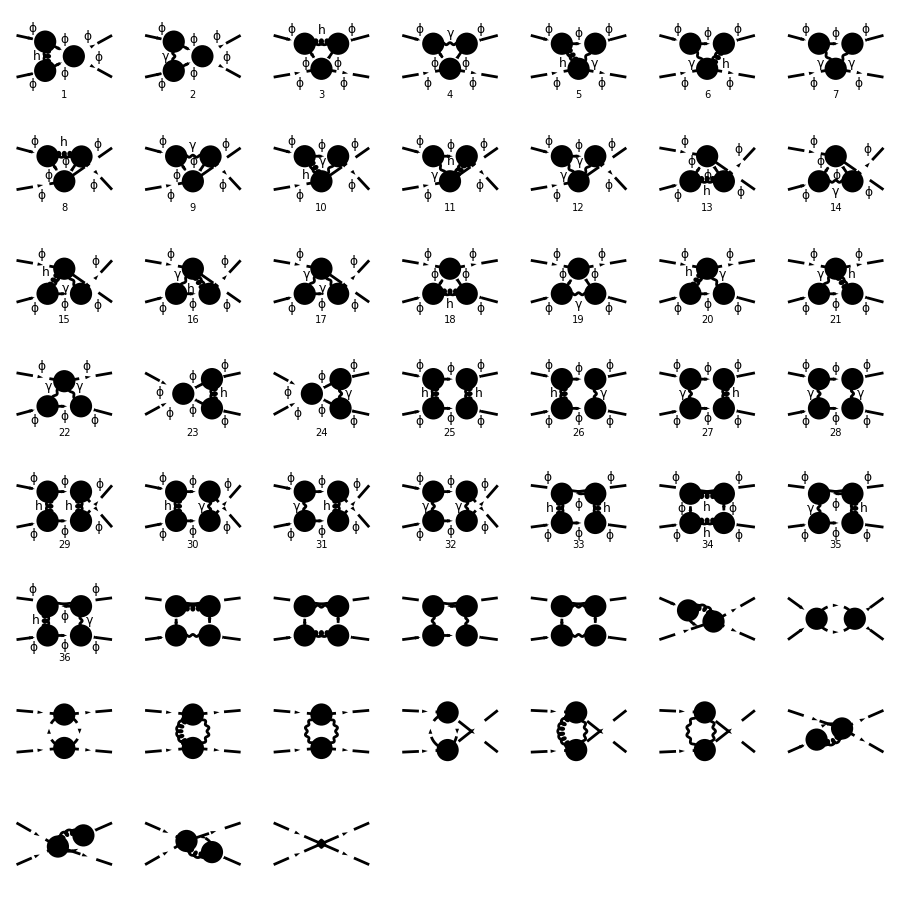

```mathematica
Paint[diag4,ColumnsXRows->{7,8},SheetHeader->{"Scalar 4-points function"},Numbering->Simple,ImageSize->{900,900}];
```

```mathematica
(*As we can see from the above diagrams, there some of then with 2 gravitons exchange. Since we are using the one-graviton exchange approximation, we remove them.*)
```

```mathematica
diagScat=DiagramDelete[diag4,{25,29,33,34}];
```

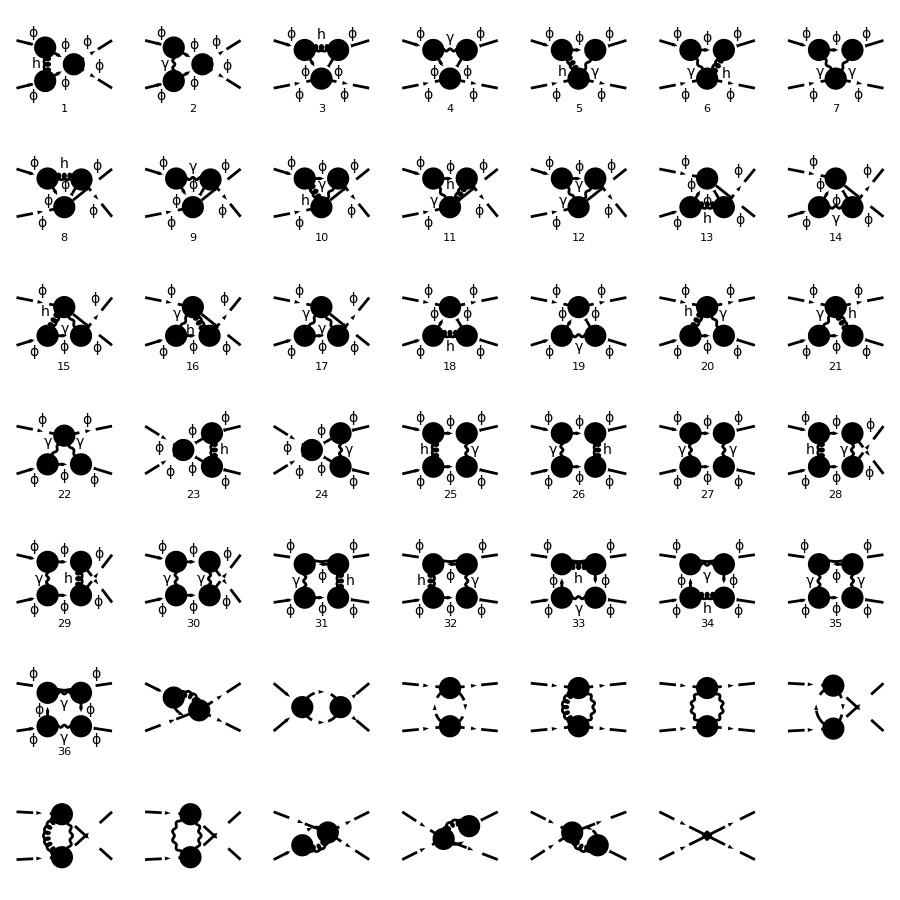

```mathematica
Paint[diagScat,ColumnsXRows->{7,7},SheetHeader->{"Scalar 4-points function"},Numbering->Simple,ImageSize->{900,900}];
```

```mathematica
(*For simplicity, we set all external momenta equal to zero.*)
```

```mathematica
ampScat[0]=FCFAConvert[CreateFeynAmp[diagScat,Truncated->True,GaugeRules->{}],IncomingMomenta->{0,0},OutgoingMomenta->{0,0},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Zl->1+δλ}]
```

-(ⅈ κ^2 ((4 (1-ξ_A) (1-ξ_h) k^6)/((k^2)^2.(k^2-m^2)^2.(k^2)^2)-((2 D-D^2) (1-ξ_A) k^4)/(2 (k^2)^2.(k^2-m^2).k^2.(k^2-m^2))-(4 (1-ξ_h) k^4)/(k^2.(k^2-m^2)^2.(k^2)^2)+((2 D-D^2) k^2)/(2 k^2.(k^2-m^2).k^2.(k^2-m^2))) e^2 m^4)/(64 π^4)-(ⅈ κ^2 ((4 (1-ξ_A) (1-ξ_h) k^6)/((k^2-m^2).(k^2)^2.(k^2-m^2).(k^2)^2)-((2 D-D^2) (1-ξ_A) k^4)/(2 k^2.(k^2-m^2).(k^2)^2.(k^2-m^2))-(4 (1-ξ_h) k^4)/((k^2-m^2).k^2.(k^2-m^2).(k^2)^2)+((2 D-D^2) k^2)/(2 k^2.(k^2-m^2).k^2.(k^2-m^2))) e^2 m^4)/(64 π^4)+(ⅈ κ^2 ((4 (1-ξ_A) (1-ξ_h) k^6)/((k^2-m^2).(k^2)^2.(k^2-m^2).(k^2)^2)-((2 D-D^2) (1-ξ_A) k^4)/(2 (k^2-m^2).(k^2)^2.(k^2-m^2).k^2)-(4 (1-ξ_h) k^4)/((k^2-m^2).k^2.(k^2-m^2).(k^2)^2)+((2 D-D^2) k^2)/(2 (k^2-m^2).k^2.(k^2-m^2).k^2)) e^2 m^4)/(64 π^4)+(ⅈ κ^2 ((4 (1-ξ_A) (1-ξ_h) k^6)/((k^2-m^2)^2.(k^2)^4)-((2 D-D^2) (1-ξ_A) k^4)/(2 (k^2-m^2).k^2.(k^2-m^2).(k^2)^2)-(4 (1-ξ_h) k^4)/((k^2-m^2)^2.(k^2)^3)+((2 D-D^2) k^2)/(2 (k^2-m^2).k^2.(k^2-m^2).k^2)) e^2 m^4)/(64 π^4)-(3 ⅈ κ^2 λ ((2 D-D^2)/(2 k^2.(k^2-m^2)^2)-(4 (1-ξ_h) k^2)/((k^2-m^2)^2.(k^2)^2)) m^4)/(32 π^4)-(ⅈ κ^2 λ ((2 D-D^2)/(2 (k^2-m^2).k^2)-(4 (1-ξ_h) k^2)/((k^2-m^2).(k^2)^2)) m^2)/(16 π^4)-(ⅈ (((1-ξ_A)^2 k^4)/((k^2)^4)-(2 (1-ξ_A) k^2)/((k^2)^3)+D/((k^2)^2)) e^4)/(4 π^4)+(ⅈ (((1-ξ_A)^2 k^6)/((k^2-m^2).(k^2)^4)-(2 (1-ξ_A) k^4)/((k^2-m^2).(k^2)^3)+k^2/((k^2-m^2).(k^2)^2)) e^4)/(2 π^4)-(3 ⅈ (((1-ξ_A)^2 k^8)/((k^2)^2.(k^2-m^2).(k^2)^2.(k^2-m^2))-((1-ξ_A) k^6)/((k^2)^2.(k^2-m^2).k^2.(k^2-m^2))-((1-ξ_A) k^6)/(k^2.(k^2-m^2).(k^2)^2.(k^2-m^2))+k^4/(k^2.(k^2-m^2).k^2.(k^2-m^2))) e^4)/(16 π^4)-(ⅈ (((1-ξ_A)^2 k^8)/((k^2-m^2).(k^2)^2.(k^2-m^2).(k^2)^2)-((1-ξ_A) k^6)/((k^2-m^2).(k^2)^2.(k^2-m^2).k^2)-((1-ξ_A) k^6)/((k^2-m^2).k^2.(k^2-m^2).(k^2)^2)+k^4/((k^2-m^2).k^2.(k^2-m^2).k^2)) e^4)/(16 π^4)+(ⅈ λ (k^2/(k^2.(k^2-m^2)^2)-((1-ξ_A) k^4)/((k^2)^2.(k^2-m^2)^2)) e^2)/(8 π^4)-λ δ_λ-(5 ⅈ λ^2)/(32 π^4 (k^2-m^2)^2)

```mathematica
(*Here, we set UsePaVeBasis->True to simplify our computation*)
ampScat[1]=TID[ampScat[0],k,ToPaVe->True,UsePaVeBasis->True]
```

(B_0(0,m^2,m^2) (16 e^4 ξ_A^2-8 e^2 λ ξ_A-3 D^2 κ^2 λ m^2+6 D κ^2 λ m^2+24 κ^2 λ m^2 ξ_h+10 λ^2-24 κ^2 λ m^2))/(64 π^2)-(e^4 B_0(0,0,0) (-ξ_A^2-D+1))/(4 π^2)+(A_0(m^2) (-32 e^4 ξ_A^2+D^2 κ^2 λ m^2-2 D κ^2 λ m^2-8 κ^2 λ m^2 ξ_h+8 κ^2 λ m^2))/(64 π^2 m^2)-λ δ_λ

```mathematica
(*Here, it is better to use PaVeUVPart instead of PaXEvaluate because we set the external momenta equal to zero. Therefore we may end with IR divergencies. Notice that such divergencies are only a consequence of our choice to set the external momenta to zero since we are only interested in the renormalization of λ, not a true divergence of the theory.*)
```

```mathematica
ampScat[2]=Simplify[(SelectNotFree2[#1,{Epsilon,δλ}]&)[Normal[(Series[#1,{Epsilon,0,0}]&)[(FCReplaceD[#1,D->4-2*Epsilon]&)[DiracSimplify[PaVeUVPart[ampScat[1]]]]]]]]
```

(-4 e^2 λ ξ_A+24 e^4+8 κ^2 λ m^2 ξ_h+5 λ^2-16 κ^2 λ m^2)/(32 π^2 ε)-λ δ_λ

```mathematica
(*Finally, we find the countertem.*)
solution5=Flatten[Solve[ampScat[2]==0,δλ]]
```

{δ_λ→(-4 e^2 λ ξ_A+24 e^4+8 κ^2 λ m^2 ξ_h+5 λ^2-16 κ^2 λ m^2)/(32 π^2 ε λ)}

```mathematica
Subscript[δ,λ]=δλ/.solution5
```

(-4 e^2 λ ξ_A+24 e^4+8 κ^2 λ m^2 ξ_h+5 λ^2-16 κ^2 λ m^2)/(32 π^2 ε λ)

#### β-functions

```mathematica
(*Now, we use our results to compute the β-functions*)
```

```mathematica
βe=Limit[μ*D[SMP["e"]*1/2*(1+Subscript[δ,A])*μ^(-2*Epsilon),μ],Epsilon->0]
```

e^3/(48 π^2)

```mathematica
βλ=Collect2[Limit[μ*D["λ"*(2*(1+Subscript[δ,ϕ])-(1+Subscript[δ,λ]))*μ^(-2*Epsilon),μ],Epsilon->0],"κ",Factoring->Expand]
```

(3 e^4)/(2 π^2)-(3 e^2 λ)/(4 π^2)+κ^2 ((λ m^2 ξ_h)/(4 π^2)-(λ m^2)/(2 π^2))+(5 λ^2)/(16 π^2)

## γ self energy 2-loops

Now we are going to compute the 2-loops photon self-energy diagrams. In order to do so, we have used TARCER.

#### Diagrams

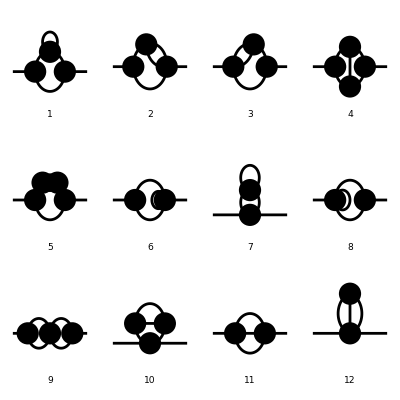

```mathematica
(*The topologies of the two-loops self-energy diagrams are the following. Notice that we have introduced diagram with 5 adjacencies because of interactions with five fields in one point, such as hϕ⁴.*)
Paint[top2l[1,1],ColumnsXRows->{4,3},SheetHeader->{"Self-energy two-loop topologies"},Numbering->Simple,ImageSize->{400,400}];
```

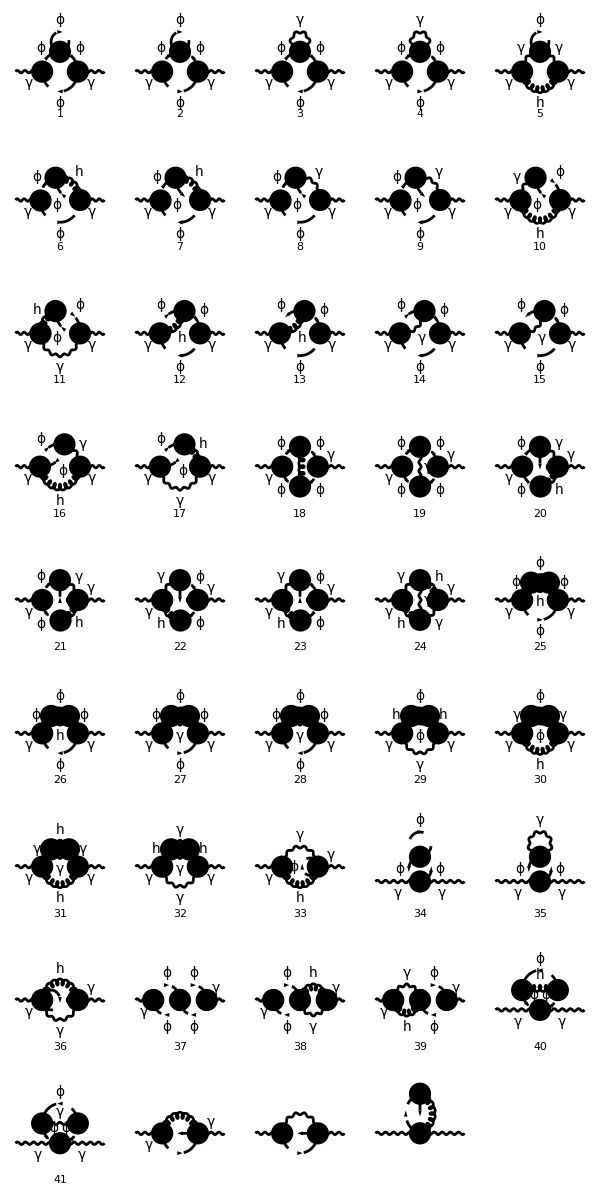

```mathematica
seph2a=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields1]&)[top2l[1,1]];
Paint[seph2a,ColumnsXRows->{5,9},SheetHeader->{"2-loops photon self-energy"},Numbering->Simple,ImageSize->{600,1200}];
```

As we can see from the figure above, there are diagrams with two gravitons, which would contribute with terms of order κ⁴, but we restrict ourselves to order κ.b2. Then, we delete those diagrams.

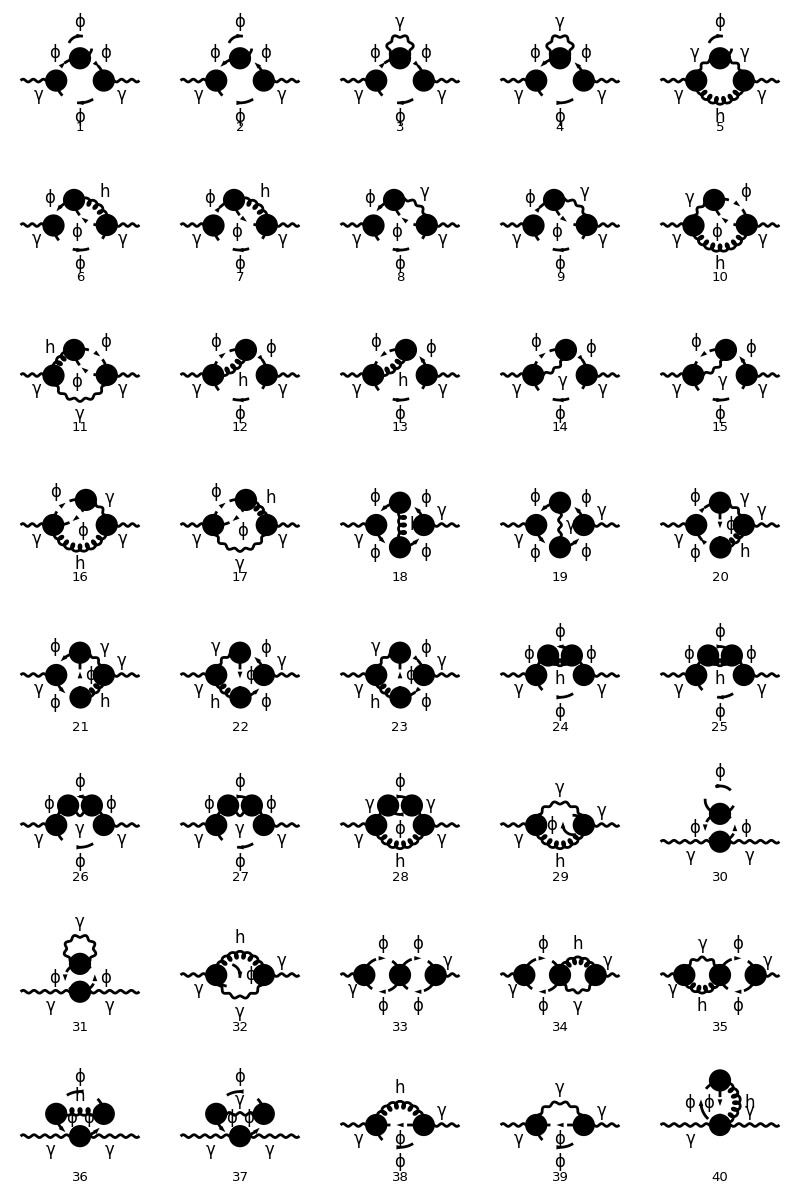

```mathematica
seph2=DiagramDelete[seph2a,{24,29,31,32}];
Paint[seph2,ColumnsXRows->{5,8},SheetHeader->{"2-loops photon self-energy"},Numbering->Simple,ImageSize->{800,1200}];
```

#### Helper functions

In this section, we create some helper functions to compute the diagrams.

```mathematica
(*The first helper function is createAmplitudes. It creates the amplitudes of a diagram from a process(such as the photon self-energy).*)
createAmplitudes[allprocesses_,diagram_]:=(Expand[Simplify[FCFAConvert[#1,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k1,k2},List->False,SMP->True,LorentzIndexNames->{mu,nu},Contract->True,ChangeDimension->D]]]&)[CreateFeynAmp[DiagramExtract[allprocesses,diagram],Truncated->True,GaugeRules->{}]]

(*Now, because TARCER can only deal with scalar integrals, we need to find a way to transform our tensorial integrals in scalar ones. To do so, we notice that our integrals can be rewritten as Π^(μν)=p^2*g^(μν)*A + p^μ*p^ν*B, where A and B are scalar integrals. Then, we find that A=1/((D-1)*p^2)*(g_(μν)-(p_μ p_ν)/p^2)*Π^(μν) and 
B=-1/((D-1)*p^2)*(g_(μν)-D*(p_μ p_ν)/p^2)*Π^(μν). Then, we define the functions findA and findB to find what are A and B for each amplitude.*) 
findA[amplitude_]:=(Expand[Simplify[DotExpand[#1]]]&)[(Contract[#1]&)[1/((D-1)*Pair[Momentum[p,D],Momentum[p,D]])*(Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]/Pair[Momentum[p,D],Momentum[p,D]])*amplitude]]
findB[amplitude_]:=(Expand[Simplify[DotExpand[#1]]]&)[(Contract[#1]&)[-1/((D-1)*Pair[Momentum[p,D],Momentum[p,D]])*(Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-D*Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]/Pair[Momentum[p,D],Momentum[p,D]])*amplitude]]

(*Now, it is important to notice that TARCER can only compute scalar integrals and can not compute amplitudes. Because of that, we must isolate the integrals and solve one by one. To do so, we first isolate the integrals in the amplitude using the function FCLoopIsolate and make a list in which each element is the part of the amplitude proportional to one specific integral, to do so we use List @@.*)
isolateIntegralsAndMakeList[scalarAmplitude_]:=Expand[List@@FCLoopIsolate[scalarAmplitude,{k1,k2},Head->loopInt]]

(*Once we have the list of integrals, we can compute then. For this, we define the function integralsCompute. The first thing we have to do is to pick one element of the list of integrals. To do so, we use the function Table. This function enables us to use an index i that goes from first one up to a desired number, in our case, this number is the length of our list of integrals. Then, we select the element of number i in our list with listOfIntegrals[[i]]. After that, we take only the integral and then set loopInt->Identity to be able to compute it. Next we convert the integrals to TARCER notation using ToTFI and use TarcerRecurse to simplify the integrals. Then, we need to coupled our simplified integral once again with the prefactors that we have discarded. Finally, after compute all the integrals, we use Plus@@ to sum all the elements in the list.*)
integralsCompute[listOfIntegrals_]:=Plus@@Table[(Expand[Simplify[#1]]&)[(listOfIntegrals[[i]]/.{Cases2[listOfIntegrals[[i]],loopInt][[1]]->#1}&)[(Expand[TarcerRecurse[#1]]&)[(ToTFI[#1,k1,k2,p]&)[(#1/.{loopInt->Identity}&)[(Cases2[#1,loopInt][[1]]&)[listOfIntegrals[[i]]]]]]]],{i,Length[listOfIntegrals]}]

(*At last, we substitute the results we have found for A and B in our expression for the tensorial amplitude.*)
findFinalResult[computedA_,computedB_]:=Expand[MTD[mu,nu]*SPD[p,p]*computedA+Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]*computedB]
```

#### Computation

In this section, we do the computation of all diagrams. As you my notice, we summed amplitudes 30, 31 and 39 with α*amplitude 1. We did this because amplitudes 30, 31 and 39 have only one term. Then, when we use List@@ in function isolateIntegralsAndMakeList, we won’t end up with a list of one element. Instead, Mathematica will make a list with all elements that are multiplied. To illustrate this, see the example below:

```mathematica
List@@(a*b)
```

{a,b}

As we can see, instead of have a list with only the element ab, we have a list with two elements, a and b. In our case, this will be a problem when we deal amplitudes with only one element, because it will split it in several parts and in the end, when we use Plus@@, we will have the wrong result in hands. See the example below,

```mathematica
List@@(MTD[mu,nu]*SMP["e"]*FAD[k,k-p])
Plus@@%
```

{1/(k^2.(k-p)^2),g^μν,e}

1/(k^2.(k-p)^2)+e+g^μν

We end up with a completely wrong result.

```mathematica
AbsoluteTiming[For[
i=1,i≤29,i++,{
amp[i]=createAmplitudes[seph2,{i}],
A[i]=findA[amp[i]],
B[i]=findB[amp[i]],
listA[i]=isolateIntegralsAndMakeList[A[i]],
listB[i]=isolateIntegralsAndMakeList[B[i]],
computedA[i]=integralsCompute[listA[i]],
computedB[i]=integralsCompute[listB[i]],
final[i]=findFinalResult[computedA[i],computedB[i]]//Expand//Simplify//Expand}
];
amp[30]=createAmplitudes[seph2,{30}]+α*createAmplitudes[seph2,{1}];
A[30]=findA[amp[30]];
B[30]=findB[amp[30]];
listA[30]=isolateIntegralsAndMakeList[A[30]];
listB[30]=isolateIntegralsAndMakeList[B[30]];
computedA[30]=integralsCompute[listA[30]];
computedB[30]=integralsCompute[listB[30]];
final[30]=Limit[findFinalResult[computedA[30],computedB[30]],α->0]//Expand//Simplify//Expand;
amp[31]=createAmplitudes[seph2,{31}]+α*createAmplitudes[seph2,{1}];
A[31]=findA[amp[31]];
B[31]=findB[amp[31]];
listA[31]=isolateIntegralsAndMakeList[A[31]];
listB[31]=isolateIntegralsAndMakeList[B[31]];
computedA[31]=integralsCompute[listA[31]];
computedB[31]=integralsCompute[listB[31]];
final[31]=Limit[findFinalResult[computedA[31],computedB[31]],α->0]//Expand//Simplify//Expand;
For[
i=32,i≤38,i++,{
amp[i]=createAmplitudes[seph2,{i}],
A[i]=findA[amp[i]],
B[i]=findB[amp[i]],
listA[i]=isolateIntegralsAndMakeList[A[i]],
listB[i]=isolateIntegralsAndMakeList[B[i]],
computedA[i]=integralsCompute[listA[i]],
computedB[i]=integralsCompute[listB[i]],
final[i]=findFinalResult[computedA[i],computedB[i]]//Expand//Simplify//Expand}
];
amp[39]=createAmplitudes[seph2,{39}]+α*createAmplitudes[seph2,{1}];
A[39]=findA[amp[39]];
B[39]=findB[amp[39]];
listA[39]=isolateIntegralsAndMakeList[A[39]];
listB[39]=isolateIntegralsAndMakeList[B[39]];
computedA[39]=integralsCompute[listA[39]];
computedB[39]=integralsCompute[listB[39]];
final[39]=Limit[findFinalResult[computedA[39],computedB[39]],α->0]//Expand//Simplify//Expand;
amp[40]=createAmplitudes[seph2,{40}];
A[40]=findA[amp[40]];
B[40]=findB[amp[40]];
listA[40]=isolateIntegralsAndMakeList[A[40]];
listB[40]=isolateIntegralsAndMakeList[B[40]];
computedA[40]=integralsCompute[listA[40]];
computedB[40]=integralsCompute[listB[40]];
final[40]=findFinalResult[computedA[40],computedB[40]]//Expand//Simplify//Expand;]
```

{3013.78,Null}

```mathematica
(*Because the result must be gauge invariant, we expect that A+B=0*)
totalA=Limit[Sum[computedA[i],{i,1,40}],α->0];
totalB=Limit[Sum[computedB[i],{i,1,40}],α->0];
totalA+totalB//Simplify//Expand
```

0

```mathematica
(*The result is gauge invariant*)
```

```mathematica
totalSum=Sum[final[i],{i,1,40}]//Expand//Simplify//Expand;
Pimunu2l=Factor[totalSum]
```

1/(49152 (D-4) (D-3) (D-2) (D-1)^2 m^2 p^2 π^8)(p^2 g^μν-p^μ p^ν) e^2 (20 κ^2 m^2 (A_{1,m}^(D))^2 D^8+κ^2 p^2 (A_{1,m}^(D))^2 D^8+κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^8-48 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^8-6 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^8-428 κ^2 m^2 (A_{1,m}^(D))^2 D^7-20 κ^2 p^2 (A_{1,m}^(D))^2 D^7-64 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D^7-8 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D^7-20 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^7-48 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^7-8 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^7-24 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^7+1512 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^7+102 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^7+384 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D^7+48 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^7+64 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^7-2 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^7-8 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^7+4344 κ^2 m^2 (A_{1,m}^(D))^2 D^6+203 κ^2 p^2 (A_{1,m}^(D))^2 D^6+192 e^2 (A_{1,m}^(D))^2 D^6-192 λ (A_{1,m}^(D))^2 D^6+768 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D^6+120 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D^6+203 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^6+768 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^6+120 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^6+192 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^6+264 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^6+12 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^6+96 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^6-96 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^6-21048 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^6-854 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^6-5248 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D^6-704 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^6-1760 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^6+36 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^6+296 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^6-512 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D) D^6+16 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D) D^6+64 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^6-26344 κ^2 m^2 (A_{1,m}^(D))^2 D^5-1264 κ^2 p^2 (A_{1,m}^(D))^2 D^5-2112 e^2 (A_{1,m}^(D))^2 D^5+2496 λ (A_{1,m}^(D))^2 D^5-2560 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D^5-744 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D^5+48 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^5+3 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^5-24 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^5-1264 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^5-5136 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^5-744 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^5-2688 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^5-696 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5+384 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5-300 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5-384 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^5+192 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^5+96 κ^2 m^2 p^4 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^5-384 κ^2 m^4 p^2 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^5-1536 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^5-384 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^5+1536 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^5+768 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^5+162168 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^5+4002 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^5-768 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^5+22016 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D^5+4704 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^5+21824 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^5-334 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^5-4120 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^5+5632 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5-208 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5-576 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5+99504 κ^2 m^2 (A_{1,m}^(D))^2 D^4+4904 κ^2 p^2 (A_{1,m}^(D))^2 D^4+9408 e^2 (A_{1,m}^(D))^2 D^4-12864 λ (A_{1,m}^(D))^2 D^4-2944 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D^4+2472 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D^4-720 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^4-45 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^4+360 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^4+4904 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^4+18624 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^4+2472 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^4+15168 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^4-2616 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4-4224 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4+2904 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4+4992 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4-384 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^4-192 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^4-2304 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^4-1152 κ^2 m^2 p^4 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^4+4608 κ^2 m^4 p^2 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^4+11040 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^4+7680 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^4-1536 κ^2 m^4 p^4 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^4-3072 κ^2 m^6 p^2 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^4-11424 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^4-12288 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^4+1536 κ^2 m^4 p^4 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^4+3072 κ^2 m^6 p^2 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^4-740632 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^4-9492 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^4+9216 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^4+2816 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D^4-18944 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^4-146464 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^4+1860 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^4+29752 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^4-14336 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4+1072 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4-1088 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4-231936 κ^2 m^2 (A_{1,m}^(D))^2 D^3-11584 κ^2 p^2 (A_{1,m}^(D))^2 D^3-22080 e^2 (A_{1,m}^(D))^2 D^3+33600 λ (A_{1,m}^(D))^2 D^3+37184 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D^3-4752 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D^3+4416 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^3+360 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^3-2496 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^3-1536 m^4 e^2 (B_({1,m}{1,m})^(D))^2 D^3+768 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2 D^3-11680 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^3-39552 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^3-4752 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^3-44160 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^3+19776 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3-96 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3+17280 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3-13056 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3-23424 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3+2688 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^3+1920 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^3+10560 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^3+5280 κ^2 m^2 p^4 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^3-21120 κ^2 m^4 p^2 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^3-44160 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^3-51840 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^3+15360 κ^2 m^4 p^4 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^3+30720 κ^2 m^6 p^2 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^3+48000 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^3+72960 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^3-15360 κ^2 m^4 p^4 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^3-30720 κ^2 m^6 p^2 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^3+2036064 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^3+5656 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^3-42240 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^3-277120 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D^3+49200 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^3+551424 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^3-6088 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^3-118592 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^3-3072 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^3+768 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^3-41984 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3-2800 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3+24384 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3+320256 κ^2 m^2 (A_{1,m}^(D))^2 D^2+15952 κ^2 p^2 (A_{1,m}^(D))^2 D^2+29184 e^2 (A_{1,m}^(D))^2 D^2-46848 λ (A_{1,m}^(D))^2 D^2-88960 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D^2+5280 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D^2-13248 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D^2-1332 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D^2+8352 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D^2+9216 m^4 e^2 (B_({1,m}{1,m})^(D))^2 D^2-4608 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2 D^2+16432 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^2+49152 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D^2+5280 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^2+69888 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D^2-47520 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2+480 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2-32640 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2+29280 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2+51840 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2-6912 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D^2-6720 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^2-23040 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^2-11520 κ^2 m^2 p^4 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^2+46080 κ^2 m^4 p^2 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D^2+98304 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^2+153600 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^2-53760 κ^2 m^4 p^4 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^2-107520 κ^2 m^6 p^2 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D^2-111744 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^2-199680 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^2+53760 κ^2 m^4 p^4 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^2+107520 κ^2 m^6 p^2 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D^2-3275904 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D^2+19856 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D^2+92160 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^2+819584 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D^2-79424 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^2-1143808 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D^2+11376 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D^2+257344 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D^2+15360 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^2-3840 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^2+257536 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2+3904 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2-86528 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2-237312 κ^2 m^2 (A_{1,m}^(D))^2 D-11648 κ^2 p^2 (A_{1,m}^(D))^2 D-20736 e^2 (A_{1,m}^(D))^2 D+33024 λ (A_{1,m}^(D))^2 D+89856 κ^2 m^2 ξ_h (A_{1,m}^(D))^2 D-3136 κ^2 p^2 ξ_h (A_{1,m}^(D))^2 D+19008 κ^2 m^6 (B_({1,m}{1,m})^(D))^2 D+2112 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2 D-12672 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2 D-16896 m^4 e^2 (B_({1,m}{1,m})^(D))^2 D+8448 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2 D-12416 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D) D-33024 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D) D-3136 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D-56832 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D) D+52224 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D-768 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D) D+28416 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D-31680 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D-54528 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D+7680 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D) D+9600 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D+23808 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D+11904 κ^2 m^2 p^4 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D-47616 κ^2 m^4 p^2 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) D-109824 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D-201216 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D+76800 κ^2 m^4 p^4 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D+153600 κ^2 m^6 p^2 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D) D+129024 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D+248832 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D-76800 κ^2 m^4 p^4 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D-153600 κ^2 m^6 p^2 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D) D+2804032 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D) D-38464 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D) D-95232 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D-961792 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D) D+70464 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D+1195648 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D) D-11072 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D) D-278336 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D) D-24576 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D+6144 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D-406016 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D) D-2752 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D) D+119040 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D+71680 κ^2 m^2 (A_{1,m}^(D))^2+3456 κ^2 p^2 (A_{1,m}^(D))^2+6144 e^2 (A_{1,m}^(D))^2-9216 λ (A_{1,m}^(D))^2-33280 κ^2 m^2 ξ_h (A_{1,m}^(D))^2+768 κ^2 p^2 ξ_h (A_{1,m}^(D))^2-10368 κ^2 m^6 (B_({1,m}{1,m})^(D))^2-1152 κ^2 m^2 p^4 (B_({1,m}{1,m})^(D))^2+6912 κ^2 m^4 p^2 (B_({1,m}{1,m})^(D))^2+9216 m^4 e^2 (B_({1,m}{1,m})^(D))^2-4608 m^2 p^2 e^2 (B_({1,m}{1,m})^(D))^2+3840 κ^2 p^4 A_{1,m}^(D) B_({1,0}{1,0})^(D)+9216 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,0}{1,0})^(D)+768 κ^2 p^4 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D)+18432 κ^2 m^2 p^2 ξ_h A_{1,m}^(D) B_({1,0}{1,0})^(D)-22272 κ^2 m^4 A_{1,m}^(D) B_({1,m}{1,m})^(D)+384 κ^2 p^4 A_{1,m}^(D) B_({1,m}{1,m})^(D)-9216 λ m^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)+13056 κ^2 m^2 p^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)+21504 m^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)-3072 p^2 e^2 A_{1,m}^(D) B_({1,m}{1,m})^(D)-4608 κ^2 m^2 p^4 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D)-9216 κ^2 m^4 p^2 B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D)-4608 κ^2 m^2 p^4 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D)+18432 κ^2 m^4 p^2 ξ_h B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D)+46080 κ^2 m^4 p^4 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)+92160 κ^2 m^6 p^2 F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)-36864 κ^2 m^4 p^4 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)-73728 κ^2 m^6 p^2 ξ_h F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)-55296 κ^2 m^4 p^4 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)-110592 κ^2 m^6 p^2 F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)+36864 κ^2 m^4 p^4 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)+73728 κ^2 m^6 p^2 ξ_h F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)-966144 κ^2 m^4 J_({1,m}{1,m}{1,0})^(D)+19200 κ^2 m^2 p^2 J_({1,m}{1,m}{1,0})^(D)+36864 m^2 e^2 J_({1,m}{1,m}{1,0})^(D)+399360 κ^2 m^4 ξ_h J_({1,m}{1,m}{1,0})^(D)-25344 κ^2 m^2 p^2 ξ_h J_({1,m}{1,m}{1,0})^(D)-476928 κ^2 m^6 J_({2,m}{1,m}{1,0})^(D)+4224 κ^2 m^2 p^4 J_({2,m}{1,m}{1,0})^(D)+113664 κ^2 m^4 p^2 J_({2,m}{1,m}{1,0})^(D)+12288 m^4 e^2 J_({2,m}{1,m}{1,0})^(D)-3072 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D)+199680 κ^2 m^6 ξ_h J_({2,m}{1,m}{1,0})^(D)+768 κ^2 m^2 p^4 ξ_h J_({2,m}{1,m}{1,0})^(D)-55296 κ^2 m^4 p^2 ξ_h J_({2,m}{1,m}{1,0})^(D))

All of this integrals are know and they can be found at [5, 6].

```mathematica
SetDirectory["/Users/lehum/Desktop/Mathematica/Results"]
```

/Users/lehum/Desktop/Mathematica/Results

```mathematica
totalA>> "totalAs.m";
totalB>> "totalBs.m";
totalSum>> "totalSums.m";
```

## Fermionic-QED

## 1-loop counterterms

Now, we show our results to the fermionic model at one-loop order.

#### Fermion self-energy

```mathematica
sefe1=(InsertFields[#1,{F[1]}->{F[1]},Sequence@@fields2]&)[top1[1,1]];
sefeCT1=(InsertFields[#1,{F[1]}->{F[1]},Sequence@@fields2]&)[topCT1[1,1]];
```

```mathematica
diag5=sefe1[[0]][Sequence@@sefe1,Sequence@@sefeCT1];
```

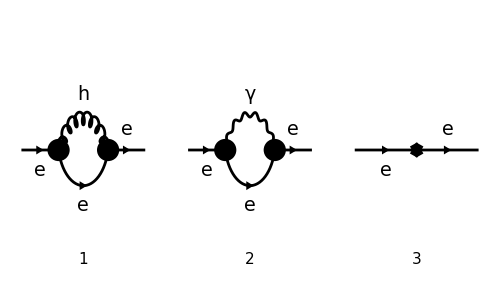

```mathematica
Paint[diag5,ColumnsXRows->{3,1},SheetHeader->{"Fermion self-energy"},Numbering->Simple,ImageSize->{500,300}];
```

```mathematica
ampfe1[0]=DiracSimplify[FCFAConvert[CreateFeynAmp[diag5,Truncated->True,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},List->False,SMP->True,ChangeDimension->D,UndoChiralSplittings->True,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z2->1+SMP["d_psi"],Zm->1+SMP["d_m"]}]]
```

(ⅈ D m p^4 κ^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^4 κ^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D p^4 κ^2 γ·k)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^4 κ^2 γ·k)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D m p^4 κ^2 ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^4 κ^2 ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D p^4 κ^2 γ·k ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^4 κ^2 γ·k ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 γ·k e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 γ·k ξ_A e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 ξ_A e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D^2 m p^2 κ^2)/(512 π^4 (k^2-m^2).(k-p)^2)-(5 ⅈ D m p^2 κ^2)/(512 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D^2 p^2 κ^2 γ·k)/(512 π^4 (k^2-m^2).(k-p)^2)+(5 ⅈ D p^2 κ^2 γ·k)/(512 π^4 (k^2-m^2).(k-p)^2)-(ⅈ p^2 κ^2 γ·k)/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m^3 p^2 κ^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^2 p^2 κ^2 γ·k)/(32 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^2 p^2 κ^2 γ·p)/(32 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^2 p^2 κ^2 γ·(p-k))/(32 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·k).(γ·p))/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·k).(γ·(p-k)))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·k).(γ·(k+p)))/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·p).(γ·k))/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·p).(γ·(p-k)))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·p).(γ·(k+p)))/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·(p-k)).(γ·k))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·(p-k)).(γ·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·(k+p)).(γ·k))/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·(k+p)).(γ·p))/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 (γ·p).(γ·k).(γ·(p-k)))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 (γ·p).(γ·k).(γ·(k+p)))/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 (γ·(p-k)).(γ·k).(γ·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 (γ·(k+p)).(γ·k).(γ·p))/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^3 p^2 κ^2 ξ_h)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^2 p^2 κ^2 γ·k ξ_h)/(32 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^2 p^2 κ^2 γ·p ξ_h)/(32 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^2 p^2 κ^2 γ·(p-k) ξ_h)/(32 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·k).(γ·p) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·k).(γ·(p-k)) ξ_h)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·k).(γ·(k+p)) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·p).(γ·k) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·p).(γ·(p-k)) ξ_h)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·p).(γ·(k+p)) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·(p-k)).(γ·k) ξ_h)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·(p-k)).(γ·p) ξ_h)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m p^2 κ^2 (γ·(k+p)).(γ·k) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m p^2 κ^2 (γ·(k+p)).(γ·p) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 (γ·p).(γ·k).(γ·(p-k)) ξ_h)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 (γ·p).(γ·k).(γ·(k+p)) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 (γ·(p-k)).(γ·k).(γ·p) ξ_h)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 (γ·(k+p)).(γ·k).(γ·p) ξ_h)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D m p^2 κ^2 k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ m p^2 κ^2 k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D p^2 κ^2 γ·k k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 γ·k k^2)/(64 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ p^2 κ^2 γ·p k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 γ·(p-k) k^2)/(64 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 γ·(k+p) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D m p^2 κ^2 ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ m p^2 κ^2 ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D p^2 κ^2 γ·k ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 γ·k ξ_h k^2)/(64 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ p^2 κ^2 γ·p ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 γ·(p-k) ξ_h k^2)/(64 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 γ·(k+p) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ m p^2 κ^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ p^2 κ^2 γ·k (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ p^2 κ^2 γ·p (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ m p^2 κ^2 ξ_h (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ p^2 κ^2 γ·k ξ_h (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ p^2 κ^2 γ·p ξ_h (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D m κ^2 k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(7 ⅈ m κ^2 k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D κ^2 γ·k k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ κ^2 γ·k k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ κ^2 γ·p k^4)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 γ·(p-k) k^4)/(64 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 γ·(k+p) k^4)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D m κ^2 ξ_h k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(7 ⅈ m κ^2 ξ_h k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D κ^2 γ·k ξ_h k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ κ^2 γ·k ξ_h k^4)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ κ^2 γ·p ξ_h k^4)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 γ·(p-k) ξ_h k^4)/(64 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 γ·(k+p) ξ_h k^4)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ κ^2 γ·p (k·p)^2)/(64 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ κ^2 γ·p ξ_h (k·p)^2)/(64 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D γ·k e^2)/(16 π^4 (k^2-m^2).(k-p)^2)+(ⅈ γ·k e^2)/(8 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D m e^2)/(16 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m (γ·k).(γ·p) e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m (γ·p).(γ·k) e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m (γ·k).(γ·p) ξ_A e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m (γ·p).(γ·k) ξ_A e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ γ·k k^2 e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ γ·p k^2 e^2)/(8 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m k^2 e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ γ·k ξ_A k^2 e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ γ·p ξ_A k^2 e^2)/(8 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m ξ_A k^2 e^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ γ·p (k·p) e^2)/(8 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ γ·p ξ_A (k·p) e^2)/(8 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ D^2 m^3 κ^2)/(128 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D m^3 κ^2)/(64 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D m^2 κ^2 γ·k)/(128 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D^2 m^2 κ^2 γ·p)/(128 π^4 (k^2-m^2).(k-p)^2)+(3 ⅈ D m^2 κ^2 γ·p)/(128 π^4 (k^2-m^2).(k-p)^2)-(ⅈ m^2 κ^2 γ·(k+p))/(64 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D^2 m κ^2 (γ·k).(γ·p))/(512 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D m κ^2 (γ·k).(γ·p))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m κ^2 (γ·k).(γ·p))/(512 π^4 (k^2-m^2).(k-p)^2)-(ⅈ m κ^2 (γ·k).(γ·(k+p)))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D^2 m κ^2 (γ·p).(γ·k))/(512 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D m κ^2 (γ·p).(γ·k))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m κ^2 (γ·p).(γ·k))/(512 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m κ^2 (γ·p).(γ·(k+p)))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ m κ^2 (γ·(k+p)).(γ·k))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m κ^2 (γ·(k+p)).(γ·p))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ κ^2 (γ·p).(γ·k).(γ·(k+p)))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ κ^2 (γ·(k+p)).(γ·k).(γ·p))/(256 π^4 (k^2-m^2).(k-p)^2)-(3 ⅈ D^2 m κ^2 k^2)/(512 π^4 (k^2-m^2).(k-p)^2)+(7 ⅈ D m κ^2 k^2)/(512 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D^2 κ^2 γ·k k^2)/(512 π^4 (k^2-m^2).(k-p)^2)-(3 ⅈ D κ^2 γ·k k^2)/(512 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D^2 κ^2 γ·p k^2)/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D κ^2 γ·p k^2)/(64 π^4 (k^2-m^2).(k-p)^2)+(ⅈ κ^2 γ·p k^2)/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ κ^2 γ·(k+p) k^2)/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ m^3 κ^2 k^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^2 κ^2 γ·k k^2)/(32 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ m^2 κ^2 γ·p k^2)/(32 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^2 κ^2 γ·(p-k) k^2)/(32 π^4 (k^2-m^2).((k-p)^2)^2)-(9 ⅈ m κ^2 (γ·k).(γ·p) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·k).(γ·(p-k)) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·k).(γ·(k+p)) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(9 ⅈ m κ^2 (γ·p).(γ·k) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·p).(γ·(p-k)) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·p).(γ·(k+p)) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·(p-k)).(γ·k) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·(p-k)).(γ·p) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·(k+p)).(γ·k) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·(k+p)).(γ·p) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 (γ·p).(γ·k).(γ·(p-k)) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 (γ·p).(γ·k).(γ·(k+p)) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 (γ·(p-k)).(γ·k).(γ·p) k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 (γ·(k+p)).(γ·k).(γ·p) k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^3 κ^2 ξ_h k^2)/(16 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^2 κ^2 γ·k ξ_h k^2)/(32 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ m^2 κ^2 γ·p ξ_h k^2)/(32 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^2 κ^2 γ·(p-k) ξ_h k^2)/(32 π^4 (k^2-m^2).((k-p)^2)^2)+(9 ⅈ m κ^2 (γ·k).(γ·p) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·k).(γ·(p-k)) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·k).(γ·(k+p)) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(9 ⅈ m κ^2 (γ·p).(γ·k) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·p).(γ·(p-k)) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·p).(γ·(k+p)) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·(p-k)).(γ·k) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·(p-k)).(γ·p) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m κ^2 (γ·(k+p)).(γ·k) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m κ^2 (γ·(k+p)).(γ·p) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 (γ·p).(γ·k).(γ·(p-k)) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 (γ·p).(γ·k).(γ·(k+p)) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 (γ·(p-k)).(γ·k).(γ·p) ξ_h k^2)/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 (γ·(k+p)).(γ·k).(γ·p) ξ_h k^2)/(256 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ D m κ^2 (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ m κ^2 (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D κ^2 γ·k (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ κ^2 γ·k (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)+(ⅈ D^2 κ^2 γ·p (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ D κ^2 γ·p (k·p))/(64 π^4 (k^2-m^2).(k-p)^2)+(ⅈ κ^2 γ·p (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ κ^2 γ·(k+p) (k·p))/(256 π^4 (k^2-m^2).(k-p)^2)-(ⅈ m^3 κ^2 (k·p))/(8 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^2 κ^2 γ·p (k·p))/(8 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ m κ^2 (γ·k).(γ·p) (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ m κ^2 (γ·p).(γ·k) (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ m^3 κ^2 ξ_h (k·p))/(8 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ m^2 κ^2 γ·p ξ_h (k·p))/(8 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ m κ^2 (γ·k).(γ·p) ξ_h (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ m κ^2 (γ·p).(γ·k) ξ_h (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(13 ⅈ m κ^2 k^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(3 ⅈ κ^2 γ·k k^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(ⅈ κ^2 γ·p k^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-(13 ⅈ m κ^2 ξ_h k^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(3 ⅈ κ^2 γ·k ξ_h k^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)+(ⅈ κ^2 γ·p ξ_h k^2 (k·p))/(128 π^4 (k^2-m^2).((k-p)^2)^2)-m δ_m+γ·p δ_ψ

```mathematica
(*Now, we use TID to convert the amplitude to the Passarino-Veltman integrals form, but before we use DiracSimplify.*)
ampfe1[1]=TID[DiracSimplify[ampfe1[0]],k,ToPaVe->True]
```

-m δ_m+γ·p δ_ψ-1/(1024 p^2 π^2)A_0(m^2) (2 D m p^2 κ^2+2 m p^2 κ^2-D^2 m^2 γ·p κ^2-2 D m^2 γ·p κ^2+2 m^2 γ·p κ^2-D^2 p^2 γ·p κ^2+2 D p^2 γ·p κ^2-6 p^2 γ·p κ^2+2 D^2 m (γ·p).(γ·p) κ^2-4 D m (γ·p).(γ·p) κ^2+10 m (γ·p).(γ·p) κ^2+6 m^2 γ·p ξ_h κ^2+6 p^2 γ·p ξ_h κ^2-12 m (γ·p).(γ·p) ξ_h κ^2+32 D γ·p e^2-64 γ·p e^2)-1/(512 p^2 π^2)B_0(0,0,0) (-D κ^2 γ·p m^4+14 κ^2 γ·p m^4+D κ^2 γ·p ξ_h m^4-14 κ^2 γ·p ξ_h m^4+2 D p^2 κ^2 m^3+24 p^2 κ^2 m^3-20 κ^2 (γ·p).(γ·p) m^3-2 D p^2 κ^2 ξ_h m^3-24 p^2 κ^2 ξ_h m^3+20 κ^2 (γ·p).(γ·p) ξ_h m^3-16 γ·p e^2 m^2+16 γ·p ξ_A e^2 m^2-16 p^2 κ^2 γ·p m^2+16 p^2 κ^2 γ·p ξ_h m^2-2 D p^4 κ^2 m+24 p^4 κ^2 m-32 p^2 e^2 m+32 (γ·p).(γ·p) e^2 m+32 p^2 ξ_A e^2 m-32 (γ·p).(γ·p) ξ_A e^2 m-28 p^2 κ^2 (γ·p).(γ·p) m+2 D p^4 κ^2 ξ_h m-24 p^4 κ^2 ξ_h m+28 p^2 κ^2 (γ·p).(γ·p) ξ_h m+16 p^2 γ·p e^2-16 p^2 γ·p ξ_A e^2+D p^4 κ^2 γ·p+2 p^4 κ^2 γ·p-D p^4 κ^2 γ·p ξ_h-2 p^4 κ^2 γ·p ξ_h)-1/(1024 p^2 π^2)B_0(p^2,0,m^2) (2 D κ^2 γ·p m^4-28 κ^2 γ·p m^4-2 D κ^2 γ·p ξ_h m^4+28 κ^2 γ·p ξ_h m^4+2 D^2 p^2 κ^2 m^3-4 D p^2 κ^2 m^3+2 p^2 κ^2 m^3+40 κ^2 (γ·p).(γ·p) m^3-12 p^2 κ^2 ξ_h m^3-40 κ^2 (γ·p).(γ·p) ξ_h m^3+32 γ·p e^2 m^2-32 γ·p ξ_A e^2 m^2+D^2 (m-p) (m+p) κ^2 γ·p m^2+2 D (m-p) (m+p) κ^2 γ·p m^2-2 (m-p) (m+p) κ^2 γ·p m^2+4 D p^2 κ^2 γ·p ξ_h m^2-8 p^2 κ^2 γ·p ξ_h m^2-6 (m-p) (m+p) κ^2 γ·p ξ_h m^2+2 D^2 p^4 κ^2 m-12 D p^4 κ^2 m+18 p^4 κ^2 m+64 D p^2 e^2 m-64 (γ·p).(γ·p) e^2 m+64 (γ·p).(γ·p) ξ_A e^2 m-4 D^2 p^2 κ^2 (γ·p).(γ·p) m+8 D p^2 κ^2 (γ·p).(γ·p) m-44 p^2 κ^2 (γ·p).(γ·p) m-2 D^2 (m-p) (m+p) κ^2 (γ·p).(γ·p) m+4 D (m-p) (m+p) κ^2 (γ·p).(γ·p) m-10 (m-p) (m+p) κ^2 (γ·p).(γ·p) m-12 p^4 κ^2 ξ_h m+48 p^2 κ^2 (γ·p).(γ·p) ξ_h m+12 (m-p) (m+p) κ^2 (γ·p).(γ·p) ξ_h m-64 D p^2 γ·p e^2+160 p^2 γ·p e^2-32 D (m-p) (m+p) γ·p e^2+64 (m-p) (m+p) γ·p e^2-32 p^2 γ·p ξ_A e^2+6 D p^4 κ^2 γ·p-4 p^4 κ^2 γ·p-D^2 (m-p) p^2 (m+p) κ^2 γ·p+6 D (m-p) p^2 (m+p) κ^2 γ·p-14 (m-p) p^2 (m+p) κ^2 γ·p-2 D p^4 κ^2 γ·p ξ_h-4 p^4 κ^2 γ·p ξ_h+6 (m-p) p^2 (m+p) κ^2 γ·p ξ_h)-1/(512 p^2 π^2)C_0(0,p^2,p^2,0,0,m^2) (2 D m κ^2 p^6-8 m κ^2 p^6-2 D κ^2 γ·p p^6+4 κ^2 γ·p p^6-2 D m κ^2 ξ_h p^6+8 m κ^2 ξ_h p^6+2 D κ^2 γ·p ξ_h p^6-4 κ^2 γ·p ξ_h p^6-4 D m^3 κ^2 p^4-32 m e^2 p^4+32 m ξ_A e^2 p^4+4 D m^2 κ^2 γ·p p^4-8 m^2 κ^2 γ·p p^4-D (m-p) (m+p) κ^2 γ·p p^4+6 (m-p) (m+p) κ^2 γ·p p^4+24 m κ^2 (γ·p).(γ·p) p^4+4 D m^3 κ^2 ξ_h p^4-4 D m^2 κ^2 γ·p ξ_h p^4+8 m^2 κ^2 γ·p ξ_h p^4+D (m-p) (m+p) κ^2 γ·p ξ_h p^4-6 (m-p) (m+p) κ^2 γ·p ξ_h p^4-24 m κ^2 (γ·p).(γ·p) ξ_h p^4+2 D m^5 κ^2 p^2+24 m^5 κ^2 p^2-32 m^3 e^2 p^2+16 (m-p) (m+p) γ·p e^2 p^2+64 m (γ·p).(γ·p) e^2 p^2+32 m^3 ξ_A e^2 p^2-16 (m-p) (m+p) γ·p ξ_A e^2 p^2-64 m (γ·p).(γ·p) ξ_A e^2 p^2-2 D m^4 κ^2 γ·p p^2+4 m^4 κ^2 γ·p p^2+2 D m^2 (m-p) (m+p) κ^2 γ·p p^2-20 m^2 (m-p) (m+p) κ^2 γ·p p^2-40 m^3 κ^2 (γ·p).(γ·p) p^2+12 m (m-p) (m+p) κ^2 (γ·p).(γ·p) p^2-2 D m^5 κ^2 ξ_h p^2-24 m^5 κ^2 ξ_h p^2+2 D m^4 κ^2 γ·p ξ_h p^2-4 m^4 κ^2 γ·p ξ_h p^2-2 D m^2 (m-p) (m+p) κ^2 γ·p ξ_h p^2+20 m^2 (m-p) (m+p) κ^2 γ·p ξ_h p^2+40 m^3 κ^2 (γ·p).(γ·p) ξ_h p^2-12 m (m-p) (m+p) κ^2 (γ·p).(γ·p) ξ_h p^2-16 m^2 (m-p) (m+p) γ·p e^2+32 m (m-p) (m+p) (γ·p).(γ·p) e^2+16 m^2 (m-p) (m+p) γ·p ξ_A e^2-32 m (m-p) (m+p) (γ·p).(γ·p) ξ_A e^2-D m^4 (m-p) (m+p) κ^2 γ·p+14 m^4 (m-p) (m+p) κ^2 γ·p-20 m^3 (m-p) (m+p) κ^2 (γ·p).(γ·p)+D m^4 (m-p) (m+p) κ^2 γ·p ξ_h-14 m^4 (m-p) (m+p) κ^2 γ·p ξ_h+20 m^3 (m-p) (m+p) κ^2 (γ·p).(γ·p) ξ_h)

```mathematica
ampfe1[2]=PaXEvaluate[ampfe1[1]]
```

1/(512 ε (m-p) (m+p) π^2)(-46 κ^2 m^5+38 κ^2 ξ_h m^5+37 κ^2 γ·p m^4-29 κ^2 γ·p ξ_h m^4+29 p^2 κ^2 m^3-32 ξ_A e^2 m^3-96 e^2 m^3+53 κ^2 (γ·p).(γ·p) m^3-16 p^2 κ^2 ξ_h m^3-46 κ^2 (γ·p).(γ·p) ξ_h m^3+32 γ·p ξ_A e^2 m^2-56 p^2 κ^2 γ·p m^2+44 p^2 κ^2 γ·p ξ_h m^2+p^4 κ^2 m+160 p^2 e^2 m-64 (γ·p).(γ·p) e^2 m-32 p^2 ξ_A e^2 m+64 (γ·p).(γ·p) ξ_A e^2 m-37 p^2 κ^2 (γ·p).(γ·p) m-6 p^4 κ^2 ξ_h m+30 p^2 κ^2 (γ·p).(γ·p) ξ_h m-32 p^2 γ·p ξ_A e^2+19 p^4 κ^2 γ·p-15 p^4 κ^2 γ·p ξ_h)+1/(512 (m-p) p^4 (m+p) π^2)(-9 κ^2 γ·p log(m^2/(m^2-p^2)) m^8+17 κ^2 γ·p ξ_h log(m^2/(m^2-p^2)) m^8-23 p^2 κ^2 log(m^2/(m^2-p^2)) m^7+27 κ^2 (γ·p).(γ·p) log(m^2/(m^2-p^2)) m^7+26 p^2 κ^2 ξ_h log(m^2/(m^2-p^2)) m^7-34 κ^2 (γ·p).(γ·p) ξ_h log(m^2/(m^2-p^2)) m^7-32 γ·p ξ_A log(m^2/(m^2-p^2)) e^2 m^6+9 p^2 κ^2 γ·p m^6-17 p^2 κ^2 γ·p ξ_h m^6-20 p^2 κ^2 γ·p ξ_h log(m^2/(m^2-p^2)) m^6-11 p^2 κ^2 γ·p log(μ^2/m^2) m^6+3 p^2 κ^2 γ·p ξ_h log(μ^2/m^2) m^6+11 p^2 κ^2 γ·p log(μ^2/(m^2 π)) m^6-3 p^2 κ^2 γ·p ξ_h log(μ^2/(m^2 π)) m^6+11 p^2 κ^2 γ·p log(π) m^6-3 p^2 κ^2 γ·p ξ_h log(π) m^6+46 ℽ p^4 κ^2 m^5-5 p^4 κ^2 m^5+160 p^2 log(m^2/(m^2-p^2)) e^2 m^5-64 (γ·p).(γ·p) log(m^2/(m^2-p^2)) e^2 m^5-32 p^2 ξ_A log(m^2/(m^2-p^2)) e^2 m^5+64 (γ·p).(γ·p) ξ_A log(m^2/(m^2-p^2)) e^2 m^5-27 p^2 κ^2 (γ·p).(γ·p) m^5-38 ℽ p^4 κ^2 ξ_h m^5+8 p^4 κ^2 ξ_h m^5+34 p^2 κ^2 (γ·p).(γ·p) ξ_h m^5-33 p^4 κ^2 log(m^2/(m^2-p^2)) m^5-11 p^2 κ^2 (γ·p).(γ·p) log(m^2/(m^2-p^2)) m^5+22 p^4 κ^2 ξ_h log(m^2/(m^2-p^2)) m^5+18 p^2 κ^2 (γ·p).(γ·p) ξ_h log(m^2/(m^2-p^2)) m^5-41 p^4 κ^2 log(μ^2/m^2) m^5+13 p^2 κ^2 (γ·p).(γ·p) log(μ^2/m^2) m^5+38 p^4 κ^2 ξ_h log(μ^2/m^2) m^5-6 p^2 κ^2 (γ·p).(γ·p) ξ_h log(μ^2/m^2) m^5-5 p^4 κ^2 log(μ^2/(m^2 π)) m^5-13 p^2 κ^2 (γ·p).(γ·p) log(μ^2/(m^2 π)) m^5+6 p^2 κ^2 (γ·p).(γ·p) ξ_h log(μ^2/(m^2 π)) m^5+41 p^4 κ^2 log(π) m^5-13 p^2 κ^2 (γ·p).(γ·p) log(π) m^5-38 p^4 κ^2 ξ_h log(π) m^5+6 p^2 κ^2 (γ·p).(γ·p) ξ_h log(π) m^5+32 p^2 γ·p ξ_A e^2 m^4+32 p^2 γ·p ξ_A log(m^2/(m^2-p^2)) e^2 m^4+32 p^2 γ·p log(μ^2/m^2) e^2 m^4-32 p^2 γ·p log(μ^2/(m^2 π)) e^2 m^4-32 p^2 γ·p log(π) e^2 m^4-37 ℽ p^4 κ^2 γ·p m^4+8 p^4 κ^2 γ·p m^4+29 ℽ p^4 κ^2 γ·p ξ_h m^4-2 p^4 κ^2 γ·p ξ_h m^4+46 p^4 κ^2 γ·p log(m^2/(m^2-p^2)) m^4-26 p^4 κ^2 γ·p ξ_h log(m^2/(m^2-p^2)) m^4+41 p^4 κ^2 γ·p log(μ^2/m^2) m^4-29 p^4 κ^2 γ·p ξ_h log(μ^2/m^2) m^4-4 p^4 κ^2 γ·p log(μ^2/(m^2 π)) m^4-41 p^4 κ^2 γ·p log(π) m^4+29 p^4 κ^2 γ·p ξ_h log(π) m^4-29 ℽ p^6 κ^2 m^3+3 p^6 κ^2 m^3+96 ℽ p^4 e^2 m^3-192 p^4 e^2 m^3+64 p^2 (γ·p).(γ·p) e^2 m^3+32 ℽ p^4 ξ_A e^2 m^3-64 p^2 (γ·p).(γ·p) ξ_A e^2 m^3-192 p^4 log(m^2/(m^2-p^2)) e^2 m^3-64 p^4 ξ_A log(m^2/(m^2-p^2)) e^2 m^3-96 p^4 log(μ^2/m^2) e^2 m^3-32 p^4 ξ_A log(μ^2/m^2) e^2 m^3+96 p^4 log(π) e^2 m^3+32 p^4 ξ_A log(π) e^2 m^3-53 ℽ p^4 κ^2 (γ·p).(γ·p) m^3+65 p^4 κ^2 (γ·p).(γ·p) m^3+16 ℽ p^6 κ^2 ξ_h m^3+8 p^6 κ^2 ξ_h m^3+46 ℽ p^4 κ^2 (γ·p).(γ·p) ξ_h m^3-70 p^4 κ^2 (γ·p).(γ·p) ξ_h m^3+23 p^6 κ^2 log(m^2/(m^2-p^2)) m^3+53 p^4 κ^2 (γ·p).(γ·p) log(m^2/(m^2-p^2)) m^3-10 p^6 κ^2 ξ_h log(m^2/(m^2-p^2)) m^3-46 p^4 κ^2 (γ·p).(γ·p) ξ_h log(m^2/(m^2-p^2)) m^3+24 p^6 κ^2 log(μ^2/m^2) m^3+40 p^4 κ^2 (γ·p).(γ·p) log(μ^2/m^2) m^3-16 p^6 κ^2 ξ_h log(μ^2/m^2) m^3-40 p^4 κ^2 (γ·p).(γ·p) ξ_h log(μ^2/m^2) m^3+5 p^6 κ^2 log(μ^2/(m^2 π)) m^3+13 p^4 κ^2 (γ·p).(γ·p) log(μ^2/(m^2 π)) m^3-6 p^4 κ^2 (γ·p).(γ·p) ξ_h log(μ^2/(m^2 π)) m^3-512 p^4 π^2 δ_m m^3-24 p^6 κ^2 log(π) m^3-40 p^4 κ^2 (γ·p).(γ·p) log(π) m^3+16 p^6 κ^2 ξ_h log(π) m^3+40 p^4 κ^2 (γ·p).(γ·p) ξ_h log(π) m^3-32 ℽ p^4 γ·p ξ_A e^2 m^2+32 p^4 γ·p ξ_A log(m^2/(m^2-p^2)) e^2 m^2-32 p^4 γ·p log(μ^2/m^2) e^2 m^2+32 p^4 γ·p ξ_A log(μ^2/m^2) e^2 m^2+32 p^4 γ·p log(μ^2/(m^2 π)) e^2 m^2+32 p^4 γ·p log(π) e^2 m^2-32 p^4 γ·p ξ_A log(π) e^2 m^2+56 ℽ p^6 κ^2 γ·p m^2-33 p^6 κ^2 γ·p m^2-44 ℽ p^6 κ^2 γ·p ξ_h m^2+33 p^6 κ^2 γ·p ξ_h m^2-56 p^6 κ^2 γ·p log(m^2/(m^2-p^2)) m^2+44 p^6 κ^2 γ·p ξ_h log(m^2/(m^2-p^2)) m^2-49 p^6 κ^2 γ·p log(μ^2/m^2) m^2+41 p^6 κ^2 γ·p ξ_h log(μ^2/m^2) m^2-7 p^6 κ^2 γ·p log(μ^2/(m^2 π)) m^2+3 p^6 κ^2 γ·p ξ_h log(μ^2/(m^2 π)) m^2+512 p^4 π^2 γ·p δ_ψ m^2+49 p^6 κ^2 γ·p log(π) m^2-41 p^6 κ^2 γ·p ξ_h log(π) m^2-ℽ p^8 κ^2 m+2 p^8 κ^2 m-160 ℽ p^6 e^2 m+192 p^6 e^2 m+64 ℽ p^4 (γ·p).(γ·p) e^2 m-64 p^4 (γ·p).(γ·p) e^2 m+32 ℽ p^6 ξ_A e^2 m-64 ℽ p^4 (γ·p).(γ·p) ξ_A e^2 m+64 p^4 (γ·p).(γ·p) ξ_A e^2 m+160 p^6 log(m^2/(m^2-p^2)) e^2 m-64 p^4 (γ·p).(γ·p) log(m^2/(m^2-p^2)) e^2 m-32 p^6 ξ_A log(m^2/(m^2-p^2)) e^2 m+64 p^4 (γ·p).(γ·p) ξ_A log(m^2/(m^2-p^2)) e^2 m+160 p^6 log(μ^2/m^2) e^2 m-64 p^4 (γ·p).(γ·p) log(μ^2/m^2) e^2 m-32 p^6 ξ_A log(μ^2/m^2) e^2 m+64 p^4 (γ·p).(γ·p) ξ_A log(μ^2/m^2) e^2 m-160 p^6 log(π) e^2 m+64 p^4 (γ·p).(γ·p) log(π) e^2 m+32 p^6 ξ_A log(π) e^2 m-64 p^4 (γ·p).(γ·p) ξ_A log(π) e^2 m+37 ℽ p^6 κ^2 (γ·p).(γ·p) m-38 p^6 κ^2 (γ·p).(γ·p) m+6 ℽ p^8 κ^2 ξ_h m-16 p^8 κ^2 ξ_h m-30 ℽ p^6 κ^2 (γ·p).(γ·p) ξ_h m+36 p^6 κ^2 (γ·p).(γ·p) ξ_h m+p^8 κ^2 log(m^2/(m^2-p^2)) m-37 p^6 κ^2 (γ·p).(γ·p) log(m^2/(m^2-p^2)) m-6 p^8 κ^2 ξ_h log(m^2/(m^2-p^2)) m+30 p^6 κ^2 (γ·p).(γ·p) ξ_h log(m^2/(m^2-p^2)) m+p^8 κ^2 log(μ^2/m^2) m-37 p^6 κ^2 (γ·p).(γ·p) log(μ^2/m^2) m-6 p^8 κ^2 ξ_h log(μ^2/m^2) m+30 p^6 κ^2 (γ·p).(γ·p) ξ_h log(μ^2/m^2) m+512 p^6 π^2 δ_m m-p^8 κ^2 log(π) m+37 p^6 κ^2 (γ·p).(γ·p) log(π) m+6 p^8 κ^2 ξ_h log(π) m-30 p^6 κ^2 (γ·p).(γ·p) ξ_h log(π) m+32 ℽ p^6 γ·p ξ_A e^2-32 p^6 γ·p ξ_A e^2-32 p^6 γ·p ξ_A log(m^2/(m^2-p^2)) e^2-32 p^6 γ·p ξ_A log(μ^2/m^2) e^2+32 p^6 γ·p ξ_A log(π) e^2-19 ℽ p^8 κ^2 γ·p+16 p^8 κ^2 γ·p+15 ℽ p^8 κ^2 γ·p ξ_h-14 p^8 κ^2 γ·p ξ_h+19 p^8 κ^2 γ·p log(m^2/(m^2-p^2))-15 p^8 κ^2 γ·p ξ_h log(m^2/(m^2-p^2))+19 p^8 κ^2 γ·p log(μ^2/m^2)-15 p^8 κ^2 γ·p ξ_h log(μ^2/m^2)-512 p^6 π^2 γ·p δ_ψ-19 p^8 κ^2 γ·p log(π)+15 p^8 κ^2 γ·p ξ_h log(π))

```mathematica
(*In order to compute the counterterm, we only need the divegent part of it*)
ampfe1[3]=SelectNotFree2[ampfe1[2],{Epsilon,SMP["d_psi"],SMP["d_m"]}]//DiracSimplify//Simplify
```

(γ·p (32 e^2 ξ_A+512 π^2 ε δ_ψ+κ^2 ξ_h (15 p^2-29 m^2)+37 κ^2 m^2-19 κ^2 p^2)+2 m (-16 e^2 ξ_A-48 e^2+κ^2 ξ_h (19 m^2-12 p^2)-23 κ^2 m^2-256 π^2 ε δ_m+18 κ^2 p^2))/(512 π^2 ε)

```mathematica
(*Finally, we solve this order by order in the external momentum*)
solution1f=Flatten[Solve[SelectFree2[Coefficient[ampfe1[3],DiracGamma[Momentum[p,D],D]],p]==0,SMP["d_psi"]]]
solution2f=Flatten[Solve[SelectFree2[ampfe1[3],{DiracGamma,p}]==0,SMP["d_m"]]]
```

{δ_ψ→(-32 e^2 ξ_A+29 κ^2 m^2 ξ_h-37 κ^2 m^2)/(512 π^2 ε)}

{δ_m→(-16 e^2 ξ_A-48 e^2+19 κ^2 m^2 ξ_h-23 κ^2 m^2)/(256 π^2 ε)}

```mathematica
Subscript[δ,ψ]=(Collect2[#1,κ,Factoring->Simplify]&)[SMP["d_psi"]/.solution1f]
Subscript[δ,mf]=(Collect2[#1,κ,Factoring->Simplify]&)[SMP["d_m"]/.solution2f]
```

(κ^2 m^2 (29 ξ_h-37))/(512 π^2 ε)-(e^2 ξ_A)/(16 π^2 ε)

(κ^2 m^2 (19 ξ_h-23))/(256 π^2 ε)-(e^2 (ξ_A+3))/(16 π^2 ε)

#### Photon self-energy

```mathematica
(*Now we proceed to compute the photon self-energy*)
```

```mathematica
sephf1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields2]&)[top1[1,1]];
sephfCT1=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields2]&)[topCT1[1,1]];
```

```mathematica
(*Here, we put together the diagrams with and without counterterms*)
diag6=sephf1[[0]][Sequence@@sephf1,Sequence@@sephfCT1];
```

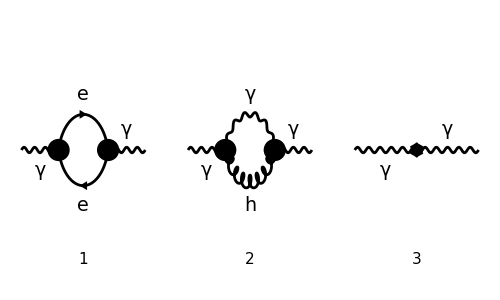

```mathematica
Paint[diag6,ColumnsXRows->{3,1},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{500,300}];
```

```mathematica
ampph[0]=FCTraceFactor[FCFAConvert[CreateFeynAmp[diag6,Truncated->True,GaugeRules->{}],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k},UndoChiralSplittings->True,List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z3->1+SMP["d_A"]}]]//DiracSimplify
```

-(ⅈ D^2 p^4 κ^2 g^μν)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ D p^4 κ^2 g^μν)/(64 π^4 k^2.(k-p)^2)-(3 ⅈ p^4 κ^2 g^μν)/(16 π^4 k^2.(k-p)^2)-(ⅈ D p^4 κ^2 k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)+(3 ⅈ p^4 κ^2 k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ D p^4 κ^2 ξ_h k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)-(3 ⅈ p^4 κ^2 ξ_h k^μ k^ν)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ p^4 κ^2 g^μν k^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ p^4 κ^2 ξ_h g^μν k^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ p^2 κ^2 g^μν k^4)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ p^2 κ^2 ξ_h g^μν k^4)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ p^2 κ^2 g^μν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ p^2 κ^2 ξ_h g^μν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ D^2 p^2 κ^2 k^μ k^ν)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ D p^2 κ^2 k^μ k^ν)/(64 π^4 k^2.(k-p)^2)-(ⅈ p^2 κ^2 k^μ k^ν)/(4 π^4 k^2.(k-p)^2)+(ⅈ D^2 p^2 κ^2 p^μ p^ν)/(128 π^4 k^2.(k-p)^2)-(7 ⅈ D p^2 κ^2 p^μ p^ν)/(64 π^4 k^2.(k-p)^2)+(3 ⅈ p^2 κ^2 p^μ p^ν)/(16 π^4 k^2.(k-p)^2)+(ⅈ p^2 κ^2 g^μν k^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ p^2 κ^2 k^μ k^ν k^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ p^2 κ^2 ξ_h k^μ k^ν k^2)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ p^2 κ^2 p^μ p^ν k^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ p^2 κ^2 ξ_h p^μ p^ν k^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ D^2 p^2 κ^2 g^μν (k·p))/(64 π^4 k^2.(k-p)^2)-(7 ⅈ D p^2 κ^2 g^μν (k·p))/(32 π^4 k^2.(k-p)^2)+(3 ⅈ p^2 κ^2 g^μν (k·p))/(8 π^4 k^2.(k-p)^2)-(ⅈ p^2 κ^2 k^μ k^ν (k·p))/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ p^2 κ^2 ξ_h k^μ k^ν (k·p))/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ D p^2 κ^2 p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(3 ⅈ p^2 κ^2 p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ D p^2 κ^2 ξ_h p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(3 ⅈ p^2 κ^2 ξ_h p^μ k^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ D p^2 κ^2 k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(3 ⅈ p^2 κ^2 k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ D p^2 κ^2 ξ_h k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(3 ⅈ p^2 κ^2 ξ_h k^μ p^ν (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ p^2 κ^2 g^μν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)-(ⅈ p^2 κ^2 ξ_h g^μν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)-g^μν δ_A p^2-(ⅈ κ^2 g^μν (k·p)^3)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h g^μν (k·p)^3)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^μ p^ν k^4)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h p^μ p^ν k^4)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ D^2 κ^2 g^μν (k·p)^2)/(128 π^4 k^2.(k-p)^2)+(7 ⅈ D κ^2 g^μν (k·p)^2)/(64 π^4 k^2.(k-p)^2)-(ⅈ κ^2 g^μν (k·p)^2)/(4 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^μ k^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h p^μ k^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 k^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h k^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)-(ⅈ D κ^2 p^μ p^ν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 p^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ D κ^2 ξ_h p^μ p^ν (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h p^μ p^ν (k·p)^2)/(8 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 g^μν k^2 (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 ξ_h g^μν k^2 (k·p)^2)/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ m^2 g^μν e^2)/(4 π^4 (k^2-m^2).((k-p)^2-m^2))+(ⅈ k^μ k^ν e^2)/(2 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ p^μ k^ν e^2)/(4 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ k^μ p^ν e^2)/(4 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ g^μν k^2 e^2)/(4 π^4 (k^2-m^2).((k-p)^2-m^2))+(ⅈ g^μν (k·p) e^2)/(4 π^4 (k^2-m^2).((k-p)^2-m^2))-(ⅈ κ^2 p^μ p^ν k^2)/(16 π^4 k^2.(k-p)^2)+(ⅈ D^2 κ^2 p^μ k^ν (k·p))/(128 π^4 k^2.(k-p)^2)-(7 ⅈ D κ^2 p^μ k^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 p^μ k^ν (k·p))/(4 π^4 k^2.(k-p)^2)+(ⅈ D^2 κ^2 k^μ p^ν (k·p))/(128 π^4 k^2.(k-p)^2)-(7 ⅈ D κ^2 k^μ p^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(ⅈ κ^2 k^μ p^ν (k·p))/(4 π^4 k^2.(k-p)^2)-(ⅈ D^2 κ^2 p^μ p^ν (k·p))/(64 π^4 k^2.(k-p)^2)+(7 ⅈ D κ^2 p^μ p^ν (k·p))/(32 π^4 k^2.(k-p)^2)-(3 ⅈ κ^2 p^μ p^ν (k·p))/(8 π^4 k^2.(k-p)^2)-(ⅈ κ^2 p^μ k^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h p^μ k^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 k^μ p^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h k^μ p^ν k^2 (k·p))/(16 π^4 (k-p)^2.(k^2)^2)-(ⅈ κ^2 p^μ p^ν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)+(ⅈ κ^2 ξ_h p^μ p^ν k^2 (k·p))/(4 π^4 (k-p)^2.(k^2)^2)+p^μ p^ν δ_A

```mathematica
ampph[1]=TID[ampph[0],k,ToPaVe->True]
```

-((2-D) κ^2 C_0(0,p^2,p^2,0,0,0) (1-ξ_h) (g^μν p^2-(1-D) p^μ p^ν-D p^μ p^ν) p^4)/(64 (1-D) π^2)+((2-D) κ^2 B_0(0,0,0) (1-ξ_h) (g^μν p^2-(1-D) p^μ p^ν-D p^μ p^ν) p^2)/(64 (1-D) π^2)+1/(512 (1-D) π^2)κ^2 B_0(p^2,0,0) (-p^μ p^ν D^3+(1-D) p^2 g^μν D^2+p^2 g^μν D^2-2 (1-D) p^μ p^ν D^2+16 ξ_h p^μ p^ν D^2-2 p^μ p^ν D^2-14 (1-D) p^2 g^μν D-30 p^2 g^μν D+16 p^2 ξ_h g^μν D+12 (1-D) p^μ p^ν D+16 (1-D) ξ_h p^μ p^ν D-64 ξ_h p^μ p^ν D+32 p^μ p^ν D+32 (1-D) p^2 g^μν+64 p^2 g^μν-32 p^2 ξ_h g^μν-32 (1-D) p^μ p^ν-32 (1-D) ξ_h p^μ p^ν+64 ξ_h p^μ p^ν-64 p^μ p^ν) p^2-(p^2 g^μν-p^μ p^ν) δ_A+(A_0(m^2) ((1-D) g^μν p^2+g^μν p^2+D p^μ p^ν-2 p^μ p^ν) e^2)/(4 (1-D) π^2 p^2)+(B_0(p^2,m^2,m^2) (-((1-D) g^μν p^4)-g^μν p^4+4 m^2 g^μν p^2+2 (1-D) p^μ p^ν p^2+D p^μ p^ν p^2-4 m^2 p^μ p^ν) e^2)/(8 (1-D) π^2 p^2)

```mathematica
(*To evaluate this result, we are using the function from FeynHelpers, PaXEvaluate*)
ampph[2]=PaXEvaluate[ampph[1]]
```

-1/(576 π^2 p^2)g^μν (576 π^2 p^4 δ_A+48 e^2 p^4 log(μ^2/m^2)+192 e^2 m^2 p^2+48 e^2 p^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))+96 e^2 m^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))-48 ℽ e^2 p^4+80 e^2 p^4-48 e^2 p^4 log(π)-18 ℽ κ^2 p^6 ξ_h+18 κ^2 p^6 ξ_h-18 κ^2 p^6 log(π) ξ_h+18 κ^2 p^6 ξ_h log(-μ^2/p^2)+12 ℽ κ^2 p^6-17 κ^2 p^6+12 κ^2 p^6 log(π)-12 κ^2 p^6 log(-μ^2/p^2))+1/(576 π^2 p^4)p^μ p^ν (576 π^2 p^4 δ_A+48 e^2 p^4 log(μ^2/m^2)+192 e^2 m^2 p^2+48 e^2 p^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))+96 e^2 m^2 √(p^2 (p^2-4 m^2)) log((√(p^4-4 m^2 p^2)+2 m^2-p^2)/(2 m^2))-48 ℽ e^2 p^4+80 e^2 p^4-48 e^2 p^4 log(π)-18 ℽ κ^2 p^6 ξ_h+18 κ^2 p^6 ξ_h-18 κ^2 p^6 log(π) ξ_h+18 κ^2 p^6 ξ_h log(-μ^2/p^2)+12 ℽ κ^2 p^6-17 κ^2 p^6+12 κ^2 p^6 log(π)-12 κ^2 p^6 log(-μ^2/p^2))-(p^2 g^μν (8 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2))/(96 π^2 ε)+(p^μ p^ν (8 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2))/(96 π^2 ε)

```mathematica
(*In order to compute the counterterm, we only need the divegent part of it*)
ampph[3]=SelectNotFree2[ampph[2],{Epsilon,SMP["d_A"]}]//Factor
```

-((p^2 g^μν-p^μ p^ν) (96 π^2 ε δ_A+8 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2))/(96 π^2 ε)

```mathematica
(*Once all terms are multiplied by Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]-Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]*Pair[Momentum[p,D],Momentum[p,D]], to compute the counterterms, we only need Π(p).*)
ampph[4]=Coefficient[ampph[3],(p^2 Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]] Pair[LorentzIndex[nu,D],Momentum[p,D]])]//Simplify
```

-(96 π^2 ε δ_A+8 e^2+3 κ^2 p^2 ξ_h-2 κ^2 p^2)/(96 π^2 ε)

```mathematica
(*Finally, we find the countertem. Here, we will only compute the counterterm for the Maxwell term. The HO counterterm can be easily computed using the terms proportional to p^2 in the above expression.*)
solution3f=Flatten[Solve[SelectFree2[ampph[4],p]==0,SMP["d_A"]]]
```

{δ_A→-e^2/(12 π^2 ε)}

```mathematica
Subscript[δ,A]=SMP["d_A"]/.solution3f
```

-e^2/(12 π^2 ε)

We can notice that there is no contribution of order κ.b2. Then, linearized gravity does not contribute to the electrical charge β-function in one-loop order.

#### Photon-Fermion vertex

```mathematica
vertex1f=(InsertFields[#1,{V[1]}->{F[1],-F[1]},Sequence@@fields2]&)[top1[1,2]];
vertexCT1f=(InsertFields[#1,{V[1]}->{F[1],-F[1]},Sequence@@fields2]&)[topCT1[1,2]];
```

```mathematica
diag7=vertex1f[[0]][Sequence@@vertex1f,Sequence@@vertexCT1f];
```

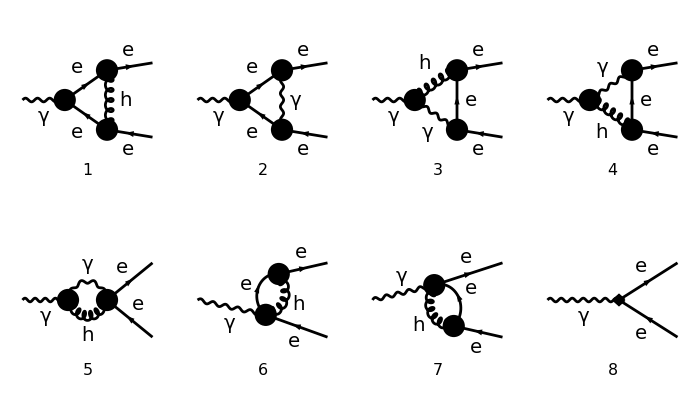

```mathematica
Paint[diag7,ColumnsXRows->{4,2},SheetHeader->{"Photon-Fermion vertex"},Numbering->Simple,ImageSize->{700,400}];
```

```mathematica
ampVertexf[0]=FCFAConvert[CreateFeynAmp[diag7,Truncated->True,GaugeRules->{}],IncomingMomenta->{p1},OutgoingMomenta->{p2,p3},LoopMomenta->{k},UndoChiralSplittings->True,List->False,SMP->True,ChangeDimension->D,LorentzIndexNames->{mu,nu},Contract->True,FinalSubstitutions->{Z1->1+SMP["d_e"]}]//DiracSimplify
```

(ⅈ D^2 m^4 κ^2 γ^μ e)/(128 π^4 (k^2-m^2).(k-p_2)^2.((k-p_2-p_3)^2-m^2))-(ⅈ D m^4 κ^2 γ^μ e)/(64 π^4 (k^2-m^2).(k-1)^2.((k-26-26)^2-m^2))+8801+1-(3 ⅈ κ^2 γ^μ ξ_h (k·26) 26^2 26^2 e)/(64 π^4 k^2.(((11)^2-m^2).(1^2)^2)-γ^μ δ_e e
 |  |  |  |

```mathematica
ampVertexf[1]=TID[ampVertexf[0],k,ToPaVe->True,UsePaVeBasis->True]
```

442+D_3(0,p_2^2,p_2^2+2 (p_2·p_3)+p_3^2,26^2,26^2,1^2,0,0,m^2,m^2) (1)
 |  |  |  |

```mathematica
(*This expression is very complicated and use PaXEvaluate to compute the integrals would take a long time. Therefore, we use here PaVeUVPart to take only the UV divergences from it*)
```

```mathematica
ampVertexf[2]=Simplify[(SelectNotFree2[#1,{Epsilon,SMP["d_e"]}]&)[Normal[(Series[#1,{Epsilon,0,0}]&)[(FCReplaceD[#1,D->4-2*Epsilon]&)[DiracSimplify[PaVeUVPart[ampVertexf[1]]]]]]]]
```

1/(3072 ε π^2)e ((234 m γ^μ.(γ·p_3)-162 m ξ_h γ^μ.(γ·p_3)-108 m (γ·p_1).γ^μ-162 m (γ·p_2).γ^μ+90 m (γ·p_3).γ^μ-6 γ^μ.(γ·p_1).(γ·p_2)+18 γ^μ.(γ·p_1).(γ·p_3)-12 γ^μ.(γ·p_2).(γ·p_1)+18 γ^μ.(γ·p_2).(γ·p_3)-144 m γ^μ.(γ·p_3).(γ̄)^6-144 m γ^μ.(γ·p_3).(γ̄)^7-24 γ^μ.(γ·p_3).(γ·p_1)+27 γ^μ.(γ·p_3).(γ·p_2)+6 (γ·p_1).γ^μ.(γ·p_2)-18 (γ·p_1).γ^μ.(γ·p_3)+12 (γ·p_1).(γ·p_2).γ^μ+24 (γ·p_1).(γ·p_3).γ^μ+144 m (γ·p_2).γ^μ.(γ̄)^6+144 m (γ·p_2).γ^μ.(γ̄)^7-36 (γ·p_2).γ^μ.(γ·p_1)-51 (γ·p_2).γ^μ.(γ·p_3)+36 (γ·p_2).(γ·p_1).γ^μ-27 (γ·p_2).(γ·p_3).γ^μ-12 (γ·p_3).γ^μ.(γ·p_1)+9 (γ·p_3).γ^μ.(γ·p_2)+12 (γ·p_3).(γ·p_1).γ^μ+30 (γ·p_3).(γ·p_2).γ^μ+144 m (γ·p_1).γ^μ ξ_h+54 m (γ·p_2).γ^μ ξ_h-90 m (γ·p_3).γ^μ ξ_h+24 γ^μ.(γ·p_1).(γ·p_2) ξ_h-24 γ^μ.(γ·p_1).(γ·p_3) ξ_h-36 γ^μ.(γ·p_2).(γ·p_3) ξ_h+72 m γ^μ.(γ·p_3).(γ̄)^6 ξ_h+72 m γ^μ.(γ·p_3).(γ̄)^7 ξ_h+48 γ^μ.(γ·p_3).(γ·p_1) ξ_h-42 γ^μ.(γ·p_3).(γ·p_2) ξ_h-24 (γ·p_1).γ^μ.(γ·p_2) ξ_h+24 (γ·p_1).γ^μ.(γ·p_3) ξ_h-48 (γ·p_1).(γ·p_3).γ^μ ξ_h-72 m (γ·p_2).γ^μ.(γ̄)^6 ξ_h-72 m (γ·p_2).γ^μ.(γ̄)^7 ξ_h+48 (γ·p_2).γ^μ.(γ·p_1) ξ_h+36 (γ·p_2).γ^μ.(γ·p_3) ξ_h-48 (γ·p_2).(γ·p_1).γ^μ ξ_h+36 (γ·p_2).(γ·p_3).γ^μ ξ_h+24 (γ·p_3).γ^μ.(γ·p_2) ξ_h-24 (γ·p_3).(γ·p_2).γ^μ ξ_h-18 m γ^μ.(γ·p_2) (ξ_h+1)-36 m γ^μ.(γ·p_1) (4 ξ_h-3)-180 m p_2^μ-144 γ·p_1 p_2^μ-40 γ·p_2 p_2^μ-112 γ·p_3 p_2^μ+48 (γ·p_2).(γ̄)^6 p_2^μ+48 (γ·p_2).(γ̄)^7 p_2^μ+180 m ξ_h p_2^μ+192 γ·p_1 ξ_h p_2^μ+72 γ·p_2 ξ_h p_2^μ+108 γ·p_3 ξ_h p_2^μ-48 (γ·p_2).(γ̄)^6 ξ_h p_2^μ-48 (γ·p_2).(γ̄)^7 ξ_h p_2^μ+36 m p_3^μ-144 γ·p_1 p_3^μ-16 γ·p_2 p_3^μ-40 γ·p_3 p_3^μ+48 (γ·p_3).(γ̄)^6 p_3^μ+48 (γ·p_3).(γ̄)^7 p_3^μ+36 m ξ_h p_3^μ+192 γ·p_1 ξ_h p_3^μ+72 γ·p_3 ξ_h p_3^μ-48 (γ·p_3).(γ̄)^6 ξ_h p_3^μ-48 (γ·p_3).(γ̄)^7 ξ_h p_3^μ+60 γ^μ.(γ̄)^6 p_2^2+60 γ^μ.(γ̄)^7 p_2^2-24 γ^μ.(γ̄)^6 ξ_h p_2^2-24 γ^μ.(γ̄)^7 ξ_h p_2^2+60 γ^μ.(γ̄)^6 p_3^2+60 γ^μ.(γ̄)^7 p_3^2-24 γ^μ.(γ̄)^6 ξ_h p_3^2-24 γ^μ.(γ̄)^7 ξ_h p_3^2) κ^2+2 γ^μ (-111 m^2 κ^2+72 (p_1·p_2) κ^2+72 (p_1·p_3) κ^2+23 p_2^2 κ^2+4 (p_2·p_3) κ^2+3 ξ_h (29 m^2-32 (p_1·p_2)-32 (p_1·p_3)-15 p_2^2-2 (p_2·p_3)-15 p_3^2) κ^2+23 p_3^2 κ^2-96 ξ_A e^2-1536 ε π^2 δ_e))

```mathematica
(*Since we are only interested in the renormalization of the gauge coupling, we discard the HO terms.*)
```

```mathematica
ampVertexf[3]=SelectFree2[ampVertexf[2],Momentum]
```

-(e^3 ξ_A γ^μ)/(16 π^2 ε)-e γ^μ δ_e+(29 e κ^2 m^2 γ^μ ξ_h)/(512 π^2 ε)-(37 e κ^2 m^2 γ^μ)/(512 π^2 ε)

```mathematica
(*Finally, we find the countertem.*)
solution7=Flatten[Solve[ampVertexf[3]==0,SMP["d_e"]]]
```

{δ_e→(-32 e^2 ξ_A+29 κ^2 m^2 ξ_h-37 κ^2 m^2)/(512 π^2 ε)}

```mathematica
Subscript[δ,e]=(Collect2[#1,κ,Factoring->Simplify]&)[SMP["d_e"]/.solution7]
```

(κ^2 m^2 (29 ξ_h-37))/(512 π^2 ε)-(e^2 ξ_A)/(16 π^2 ε)

```mathematica
(*As we can see, this is equal to the counterterm for the scalar wave function. Therefore, the Ward identity is respected*)
```

```mathematica
Subscript[δ,ψ]
```

(κ^2 m^2 (29 ξ_h-37))/(512 π^2 ε)-(e^2 ξ_A)/(16 π^2 ε)

#### β-functions

```mathematica
(*Now, we use our results to compute the β-functions*)
```

```mathematica
βe=Limit[μ*D[SMP["e"]*1/2*(1+Subscript[δ,A])*μ^(-2*Epsilon),μ],Epsilon->0]
```

e^3/(12 π^2)

## γ self energy 2-loops

In the fermionic case, we will follow the same procedure that we did before in the scalar case.

#### Diagrams

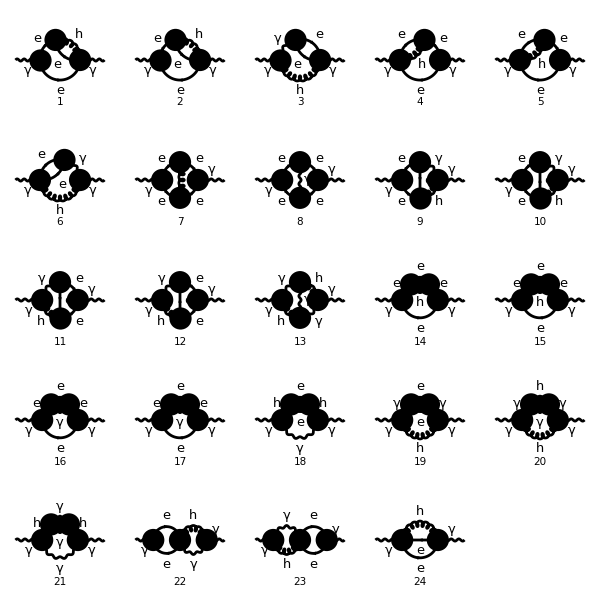

```mathematica
sephF2=(InsertFields[#1,{V[1]}->{V[1]},Sequence@@fields2]&)[top2l[1,1]];
Paint[sephF2,ColumnsXRows->{5,5},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{600,600}];
```

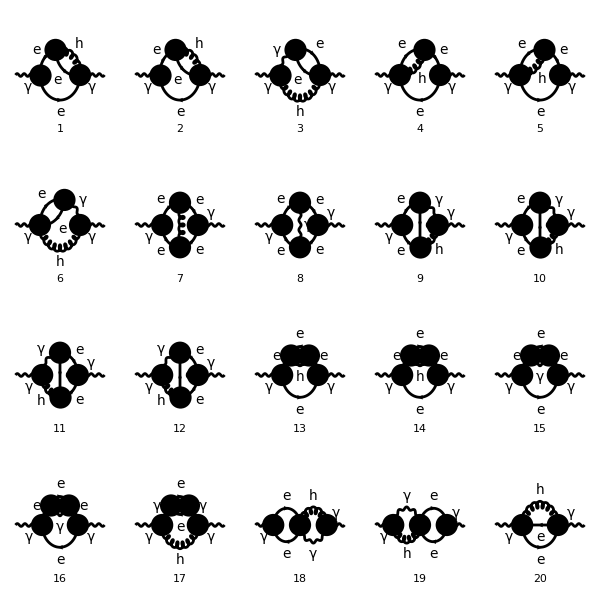

```mathematica
sephF2a=DiagramDelete[sephF2,{13,18,20,21}];
Paint[sephF2a,ColumnsXRows->{5,4},SheetHeader->{"Photon self-energy"},Numbering->Simple,ImageSize->{600,600}];
```

#### Helper functions

In this section, we create some helper functions to compute the diagrams.

```mathematica
(*The first helper function is createAmplitudes. It creates the amplitudes of a diagram from a process(such as the photon self-energy).*)
createAmplitudes[allprocesses_,diagram_]:=(Expand[Simplify[FCFAConvert[#1,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k1,k2},List->False,SMP->True,LorentzIndexNames->{mu,nu},Contract->True,ChangeDimension->D]]]&)[CreateFeynAmp[DiagramExtract[allprocesses,diagram],Truncated->True,GaugeRules->{}]]

(*Now, because TARCER can only deal with scalar integrals, we need to find a way to transform our tensorial integrals in scalar ones. To do so, we notice that our integrals can be rewritten as Π^(μν)=p^2*g^(μν)*A + p^μ*p^ν*B, where A and B are scalar integrals. Then, we find that A=1/((D-1)*p^2)*(g_(μν)-(p_μ p_ν)/p^2)*Π^(μν) and 
B=-1/((D-1)*p^2)*(g_(μν)-D*(p_μ p_ν)/p^2)*Π^(μν). Then, we define the functions findA and findB to find what are A and B for each amplitude.*) 
findA[amplitude_]:=(Expand[Simplify[DotExpand[#1]]]&)[(Contract[#1]&)[1/((D-1)*Pair[Momentum[p,D],Momentum[p,D]])*(Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]/Pair[Momentum[p,D],Momentum[p,D]])*amplitude]]
findB[amplitude_]:=(Expand[Simplify[DotExpand[#1]]]&)[(Contract[#1]&)[-1/((D-1)*Pair[Momentum[p,D],Momentum[p,D]])*(Pair[LorentzIndex[mu,D],LorentzIndex[nu,D]]-D*Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]/Pair[Momentum[p,D],Momentum[p,D]])*amplitude]]

(*Now, it is important to notice that TARCER can only compute scalar integrals and can not compute amplitudes. Because of that, we must isolate the integrals and solve one by one. To do so, we first isolate the integrals in the amplitude using the function FCLoopIsolate and make a list in which each element is the part of the amplitude proportional to one specific integral, to do so we use List @@.*)
isolateIntegralsAndMakeList[scalarAmplitude_]:=Expand[List@@FCLoopIsolate[scalarAmplitude,{k1,k2},Head->loopInt]]

(*Once we have the list of integrals, we can compute then. For this, we define the function integralsCompute. The first thing we have to do is to pick one element of the list of integrals. To do so, we use the function Table. This function enables us to use an index i that goes from first one up to a desired number, in our case, this number is the length of our list of integrals. Then, we select the element of number i in our list with listOfIntegrals[[i]]. After that, we take only the integral and then set loopInt->Identity to be able to compute it. Next we convert the integrals to TARCER notation using ToTFI and use TarcerRecurse to simplify the integrals. Then, we need to coupled our simplified integral once again with the prefactors that we have discarded. Finally, after compute all the integrals, we use Plus@@ to sum all the elements in the list.*)
integralsCompute[listOfIntegrals_]:=Plus@@Table[(Expand[Simplify[#1]]&)[(listOfIntegrals[[i]]/.{Cases2[listOfIntegrals[[i]],loopInt][[1]]->#1}&)[(Expand[TarcerRecurse[#1]]&)[(ToTFI[#1,k1,k2,p]&)[(#1/.{loopInt->Identity}&)[(Cases2[#1,loopInt][[1]]&)[listOfIntegrals[[i]]]]]]]],{i,Length[listOfIntegrals]}]

(*At last, we substitute the results we have found for A and B in our expression for the tensorial amplitude.*)
findFinalResult[computedA_,computedB_]:=Expand[MTD[mu,nu]*SPD[p,p]*computedA+Pair[LorentzIndex[mu,D],Momentum[p,D]]*Pair[LorentzIndex[nu,D],Momentum[p,D]]*computedB]
```

#### Computation

Now, we are going to use the same helper functions we defined before. We just need to use one additional function, which is DiracSimplify, once we are dealing with fermions.

```mathematica
AbsoluteTiming[For[
i=1,i≤20,i++,{
amp[i]=createAmplitudes[sephF2a,{i}],
ampD[i]=DiracSimplify[amp[i]],
A[i]=findA[ampD[i]],
B[i]=findB[ampD[i]],
listA[i]=isolateIntegralsAndMakeList[A[i]],
listB[i]=isolateIntegralsAndMakeList[B[i]],
computedA[i]=integralsCompute[listA[i]],
computedB[i]=integralsCompute[listB[i]],
final[i]=findFinalResult[computedA[i],computedB[i]]//Expand//Simplify//Expand}
];]
```

{5545.76,Null}

```mathematica
totalA=Sum[computedA[i],{i,1,20}];
totalB=Sum[computedB[i],{i,1,20}];
totalA+totalB//Simplify//Expand
```

0

```mathematica
(*The result is gauge invariant*)
```

```mathematica
totalSum=Sum[final[i],{i,1,20}]/.{Beta-> EulerGamma}//Expand//Simplify//Expand;
Pimunu2l=Factor[totalSum]//Simplify
```

((p^2 g^μν-p^μ p^ν) e^2 (-(-48 (D^4-10 D^3+35 D^2-50 D+24) p^2 (4 m^2-p^2) (-4 (D-2) m^2-(D^2-4 D+6) p^2+2 (D-2) (4 m^2+(D-2) p^2) ξ_h) B_({1,0}{1,0})^(D) B_({1,m}{1,m})^(D) κ^2+3 (D^2-5 D+6) ((64 (D^2-2 D+4) m^6+16 (D^4-12 D^3+32 D^2-14 D-16) p^2 m^4-4 (4 D^4-38 D^3+125 D^2-132 D+32) p^4 m^2+(3 D^4-22 D^3+72 D^2-88 D+32) p^6) κ^2-64 (D-1) (32 m^4+4 (D^3-11 D^2+38 D-40) p^2 m^2-(D^3-9 D^2+30 D-32) p^4) e^2) (B_({1,m}{1,m})^(D))^2+4 (D-1) (-48 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^7-3 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^7+24 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D^7+1504 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^6+64 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^6-632 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D^6+384 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^6+24 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^6-192 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^6+64 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^6-p^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^6+12 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D) D^6-48 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D) D^6-20256 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^5-783 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^5+7908 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D^5-384 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^5+96 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^5-4864 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^5-232 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^5+2432 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^5-1856 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^5+17 p^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^5-252 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D) D^5+1200 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D) D^5-512 m^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5+8 p^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5-96 m^2 p^4 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5+384 m^4 p^2 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^5+147008 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^4+5458 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^4-55296 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D^4+4608 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^4-1152 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^4+17152 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^4+584 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^4-9984 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^4+22336 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^4-138 p^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^4+2908 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D) D^4-13856 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D) D^4+1536 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^4+96 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^4-768 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^4+5120 m^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4-96 p^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4+704 m^2 p^4 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4-3712 m^4 p^2 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^4-612112 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^3-21404 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^3+224004 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D^3-21120 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^3+5280 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^3+19968 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^3+1096 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^3+5888 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^3-137408 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^3+672 p^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^3-17492 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D) D^3+83488 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D) D^3-16896 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^3-864 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^3+7680 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^3-9216 m^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3+440 p^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3-544 m^2 p^4 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3+7808 m^4 p^2 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^3+1458560 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^2+46768 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D^2-520152 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D^2+46080 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^2-11520 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D^2-257152 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^2-7904 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^2+62400 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D^2+448128 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^2-1880 p^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D^2+53848 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D) D^2-265664 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D) D^2+64512 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^2+3072 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D^2-28416 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D^2-51200 m^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2-960 p^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2-7232 m^2 p^4 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2+23680 m^4 p^2 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D^2-1845376 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D-53104 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D) D+641168 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D) D-47616 m^2 e^2 J_({1,m}{1,m}{1,0})^(D) D+11904 p^2 e^2 J_({1,m}{1,m}{1,0})^(D) D+562432 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D+13728 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D-160384 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D) D-731776 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D+2704 p^6 κ^2 J_({2,m}{1,m}{1,0})^(D) D-80688 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D) D+420672 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D) D-104448 m^4 e^2 J_({2,m}{1,m}{1,0})^(D) D-4992 p^4 e^2 J_({2,m}{1,m}{1,0})^(D) D+46080 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D) D+206336 m^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D+992 p^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D+20992 m^2 p^4 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D-106496 m^4 p^2 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D) D+12 (D^3-9 D^2+26 D-24) p^2 (4 m^2-p^2) κ^2 (4 (D^3-7 D^2+4 D+28) m^4-(D^3-7 D^2+19 D-54) p^2 m^2+2 (D-2) p^4+4 (8 (D-4) m^4+(D-10) p^2 m^2) ξ_h) F_({1,0}{1,m}{1,0}{1,m}{1,m})^(D)-12 (D^3-9 D^2+26 D-24) p^2 (p^2-4 m^2) κ^2 (-4 (D^3-7 D^2+2 D+32) m^4+(D^3-6 D^2+11 D-38) p^2 m^2-2 (D-2) p^4-4 (8 (D-4) m^4+(D-10) p^2 m^2) ξ_h) F_({1,m}{1,0}{1,m}{1,0}{1,m})^(D)+959232 m^4 κ^2 J_({1,m}{1,m}{1,0})^(D)+24384 p^4 κ^2 J_({1,m}{1,m}{1,0})^(D)-324672 m^2 p^2 κ^2 J_({1,m}{1,m}{1,0})^(D)+18432 m^2 e^2 J_({1,m}{1,m}{1,0})^(D)-4608 p^2 e^2 J_({1,m}{1,m}{1,0})^(D)-399360 m^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D)-8064 p^4 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D)+118272 m^2 p^2 κ^2 ξ_h J_({1,m}{1,m}{1,0})^(D)+467712 m^6 κ^2 J_({2,m}{1,m}{1,0})^(D)-1536 p^6 κ^2 J_({2,m}{1,m}{1,0})^(D)+46656 m^2 p^4 κ^2 J_({2,m}{1,m}{1,0})^(D)-259968 m^4 p^2 κ^2 J_({2,m}{1,m}{1,0})^(D)+61440 m^4 e^2 J_({2,m}{1,m}{1,0})^(D)+3072 p^4 e^2 J_({2,m}{1,m}{1,0})^(D)-27648 m^2 p^2 e^2 J_({2,m}{1,m}{1,0})^(D)-199680 m^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D)-384 p^6 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D)-16896 m^2 p^4 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D)+102912 m^4 p^2 κ^2 ξ_h J_({2,m}{1,m}{1,0})^(D))) m^2-2 (D-2) ((8 (2 D^7-59 D^6+716 D^5-4522 D^4+15751 D^3-30098 D^2+29168 D-10976) m^4-2 (4 D^7-92 D^6+1041 D^5-6331 D^4+21320 D^3-39512 D^2+37312 D-13760) p^2 m^2+(D-2)^2 (D^5-14 D^4+95 D^3-326 D^2+532 D-288) p^4) κ^2-8 (D-2)^2 (D-1) (16 (D^3-5 D^2-13 D+65) m^4-8 (D^3-5 D^2-3 D+31) p^2 m^2+(D^3-8 D^2+19 D-12) p^4) ξ_h κ^2+96 (D-2)^2 (D-1) (4 (D^3-7 D^2+16 D-14) m^2+(D^2-5 D+8) p^2) e^2) (A_{1,m}^(D))^2-2 (D-2) A_{1,m}^(D) ((D-2)^2 (D^3-8 D^2+19 D-12) p^2 (p^2-4 m^2) (24 (D-2) m^2+(D^2-6 D+28) p^2-8 (12 m^2+(D-1) p^2) ξ_h) B_({1,0}{1,0})^(D) κ^2+6 ((8 (D^5-11 D^4+45 D^3-95 D^2+112 D-64) m^6+2 (D^6-11 D^5+87 D^4-497 D^3+1540 D^2-2184 D+1088) p^2 m^4-(D^5-3 D^4-68 D^3+396 D^2-704 D+384) p^4 m^2-4 (D-2)^3 (D-1) p^6) κ^2-16 (D^2-3 D+2) (8 (D^3-6 D^2+5 D+8) m^4+2 (D-4)^2 (D^2-4 D+3) p^2 m^2+(D^3-7 D^2+18 D-16) p^4) e^2) B_({1,m}{1,m})^(D))))/(24576 (D-4) (D-3) (D-2) (D-1)^2 m^2 (2 m-p) p^2 (2 m+p) π^8)

All of this integrals are know and they can be found at [5, 6].

```mathematica
SetDirectory["/Users/lehum/Desktop/Mathematica/Results"]
```

/Users/lehum/Desktop/Mathematica/Results

```mathematica
totalA>> "totalAf.m";
totalB>> "totalBf.m";
totalSum>> "totalSumf.m";
```

## References

[1] V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407
[2] T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260
[3] V. Shtabovenko, Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793
[4] R. Mertig and R. Scharf, Comput. Phys. Commun., 111, 265-273, 1998, arXiv:hep-ph/9801383
[5] Stephen P. Martin and David G. Robertson, Comput. Phys. Commun., 174, 133-151, 2006, arXiv:hep-ph/0501132
[6] Stephen P. Martin, Phys. Rev. D, 68, 075002, 2003, arXiv:hep-ph/0307101